```mathematica
(**This code includes the modules for vibration analysis of a rotating tapered 2D Timoshenko Beam using finite beam element method
The method is outlined in the paper 
A.Bazoune and Y.A.Khulief,“A finite beam element for vibration analysis of rotating tapered timoshenko beams,” J.Sound Vib.,vol.156,no.1,pp.141–164,1992,doi:10.1016/0022-460X(92)90817-H.
**)
```

```mathematica
(*The code implements the finite element analysis in modules
Then generates analytical expressions for the stiffness matrices
This also inlcude a function to calculate the natural frequencies of beam for both Euler and Timoshenbko theory
Some of the results that are presented here  are as follows:
Table 6 for different taper ratios represent the 1st 10

Table 1: Cantilever - Euler-Bernoulli Beam - uniform (vy=vz=0.0)
Table 2: Cantilever - Euler-Bernoulli Beam - tapered (vy=vz=0.1)
Table 3: Cantilever - Euler-Bernoulli Beam - tapered (vy=vz=0.3)
Table 4: Cantilever - Euler-Bernoulli Beam - tapered (vy=vz=0.5)
Table 5: Cantilever - Euler-Bernoulli Beam - tapered (vy=vz=0.6)
Table 6: Cantilever - Euler-Bernoulli Beam - tapered (vy=vz=0.8)

Figures (speed ratio vs frequency) first 6th modes
Fig 1: Cantilever - Euler-Bernoulli and Timoshemko Beams - uniform (vy=vz=0.0) 
Fig 2: Cantilever - Euler-Bernoulli and Timoshemko Beams - tapered (vy=vz=0.2) 
Fig 3: Cantilever - Euler-Bernoulli and Timoshemko Beams - tapered (vy=vz=0.5) 
Fig 4: Cantilever - Euler-Bernoulli and Timoshemko Beams - tapered (vy=vz=0.7) 

Figures (taper ratio vs frequency) first 6th modes at fixed speed
Fig 5: Cantilever - Euler-Bernoulli and Timoshemko Beams - η = 0 (non rotating) 
Fig 6: Cantilever - Euler-Bernoulli and Timoshemko Beams - η = 2.0
Fig 7: Cantilever - Euler-Bernoulli and Timoshemko Beams - η = 5.0
Fig 8: Cantilever - Euler-Bernoulli and Timoshemko Beams - η = 10.0
*)
```

## Finite element formulation

## Centrifugally stiffened tapered beam element

It is assumed that the axis of the beam is straight, and deformation is confined to shear and bending in the direction of the longitudinal axis. The latter assumption eliminates torsion due to bending. Assuming that the elastic beam is aligned along the longitudinal axis in the undeformed state, one can describe the local co-ordinate vector of an arbitrary point p^i on element i with respect to the element axes, shown in Figure below, as 

{w^i}=[N_w^i]{q^i}  
{θ^i}=[N_θ^i]{q^i}  

where {q^i} is a vector of nodal co-ordinates of the beam element, and deformations are confined to one plane.

Mathematica has the capability to handle symbolic calculation. The shape function in paper is used as is.

Note: different shape functions options (2d or 3d)

```mathematica
Nv1[xi_]:= (1-3 ζ[xi]^2+2 ζ[xi]^3+Φz (1-ζ[xi]))/(1+Φz);
Nv2[xi_]:=  li (ζ[xi]-2 ζ[xi]^2+ζ[xi]^3+(ζ[xi]-ζ[xi]^2) Φz/2) /(1+Φz);
Nv3[xi_]:= (3 ζ[xi]^2-2 ζ[xi]^3+Φz ζ[xi])/(1+Φz);
Nv4[xi_]:= li (-ζ[xi]^2 +ζ[xi]^3+ (-ζ[xi]+ζ[xi]^2) Φz/2)/(1+Φz);

Nuz1[xi_]:= 6 (-ζ[xi]+ζ[xi]^2)/(li (1+Φz));
Nuz2[xi_]:= (1-4 ζ[xi]+3 ζ[xi]^2+Φz (1-ζ[xi]))/(1+Φz);
Nuz3[xi_]:=-6 (-ζ[xi]+ζ[xi]^2)/(li (1+Φz));
Nuz4[xi_]:= (-2 ζ[xi]+3 ζ[xi]^2+Φz ζ[xi])/(1+Φz);

Nw1[xi_]:=(1-3 ζ[xi]^2+2 ζ[xi]^3+(1-ζ[xi]) Φy)/(1+Φy);
Nw2[xi_]:=-(ζ[xi]-2 ζ[xi]^2+ζ[xi]^3+(ζ[xi]-ζ[xi]^2) Φy/2) li/(1+Φy);
Nw3[xi_]:=(3 ζ[xi]^2 - 2 ζ[xi]^3+ζ[xi] Φy)/(1+Φy);
Nw4[xi_]:=-(-ζ[xi]^2+ζ[xi]^3-(ζ[xi]-ζ[xi]^2) Φy/2) li/(1+Φy);

Nuy1[xi_]:=6 (-ζ[xi]+ζ[xi]^2)/(li (1+Φy));
Nuz2[xi_]:= -(1-4 ζ[xi]+3 ζ[xi]^2+Φy (1-ζ[xi]))/(1+Φy);
Nuz3[xi_]:=-6 (-ζ[xi]+ζ[xi]^2)/(li (1+Φy));
Nuz4[xi_]:= -(-2 ζ[xi]+3 ζ[xi]^2+Φy ζ[xi])/(1+Φy);
```

```mathematica
(***Thias function calculates the 4th order shape function as mentioned in the paper for an Beam**)
Clear[ComputeShapeN,Φ];
ComputeShapeN[li_,Φ_]:=Module[{psis},Clear[ζ,Nw1,Nw2,Nw3,Nw4,Nw,Nθ1,Nθ2,Nθ3,Nθ4,Nθ];
(*Φ=12 Ei Ix/(ki Gi A li^2)tim;*)ζ[xi_]:=xi/li;
Nw1[xi_]:=(1-3 ζ[xi]^2+2 ζ[xi]^3+(1-ζ[xi]) Φ)/(1+Φ);
Nw2[xi_]:=(ζ[xi]-2 ζ[xi]^2+ζ[xi]^3+(ζ[xi]-ζ[xi]^2) Φ/2) li/(1+Φ);
Nw3[xi_]:=(3 ζ[xi]^2 - 2 ζ[xi]^3+ζ[xi] Φ)/(1+Φ);
Nw4[xi_]:=(-ζ[xi]^2+ζ[xi]^3-(ζ[xi]-ζ[xi]^2) Φ/2) li/(1+Φ);
Nθ1[xi_]:=6 (-ζ[xi]+ζ[xi]^2)/(li (1+Φ));
Nθ2[xi_]:=(1-4 ζ[xi]+3 ζ[xi]^2+(1-ζ[xi]) Φ)/(1+Φ);
Nθ3[xi_]:=6 (ζ[xi]-ζ[xi]^2)/(li (1+Φ));
Nθ4[xi_]:=(-2 ζ[xi]+3 ζ[xi]^2+ζ[xi] Φ)/(1+Φ);
Nw[xi_]={{Nw1[xi],Nw2[xi],Nw3[xi],Nw4[xi]}};
Nθ[xi_]={{Nθ1[xi],Nθ2[xi],Nθ3[xi],Nθ4[xi]}};
psis=Join[ Transpose[Nw[xi]],Transpose[Nθ[xi]]];
Clear[ζ];
Return[psis]];
```

Φ 	:	shear deformation parameter (the ratio between the bending stiffness and the shear stiffness) 
E^i 	:	modulus of rigidity
I_x^i 	:  	second moment of the cross-sectional area
A_x^i 	: 	the cross-sectional area of the beam element
l^i	:	element length
G^i	:	shear modulus
k^('i)	:	shear correction factor depending on the shape of the cross-section.

## Geometrical Properties of the cross-sectional area

In order to define the entries of the stiffness and mass matrices one need to introduce the following parameters:

pr is only to hold the numerical values as an replacement rule. The symbolic variables νy1 and νz1 are used instead of νy and νz. The numerical values are substituted after symbolic substitution. This avoids getting singularity when the taper ratios take value of 0.

```mathematica
ClearAll[GenGeomParameters];
(*options argument is optional, default it will evaluate numerically except when {Symbolic->True}is passed for use in printing matrices*)
GenGeomParameters[νy_,νz_,a_,L_,n_,options_:{Symbolic->False}]:=Module[{},pr={νy1->νy,νz1->νz};
(***basic paramters in terms of element no i and (L, n->nelement)***)
lengths0={L0y->L/νy1,L0z->L/νz1,li->L/n};
lengths1={Liy->L0y-Li,Liz->L0z-Li}/.Li->(i-1)li;
(*definition of variables for matrices*)
mus={μ1->Liy Liz,μ2->(Liy+Liz)/2}/.lengths1/.lengths0;
alphas={α0->μ1 Liz^2,α1->Liz^3+3μ1 Liz,α2->6 μ2 Liz,α3->2 (Liz+μ2)}/.mus/.lengths1/.lengths0;
betas={β0->1/2 μ1 li^2(n^2-i^2+2i-1)-2/3μ2 li^3(n^3-i^3+3/2 i-1/2)+1/4 li^4(n^4-i^4+4/3 i-1/3),β1->μ1 Li,
β2->1/2(μ1-2μ2 Li),β3->1/3(Li-2μ2),β4->1/4}/.Li->(i-1)li/.mus/.lengths1/.lengths0;
A[xi_]=((A0/(L0y L0z)) (μ1 -2 μ2 xi+xi^2)/.mus/.lengths0//Simplify)/.pr//Chop//Simplify;
Ix[xi_]=((I0/(L0y L0z^3)) (α0-α1 xi+α2 xi^2-α3 xi^3+xi^4)/.alphas/.lengths0//Simplify)/.pr//Chop//Simplify;
(***if symbolic *)
If[(Symbolic/.options),
Clear[A,Ix];A[xi_]:=(A0/(L0y L0z)) (μ1 -2 μ2 xi+xi^2);
Ix[xi_]:=(I0/(L0y L0z^3)) (α0-α1 xi+α2 xi^2-α3 xi^3+xi^4);
];
(**slenderness ratio a=(rg/L*)
r2={I0->A0 a^2 L^2};
]
```

```mathematica
(***This module calculates phi value for ith element of the beam
as a function of element number i and xi * this is required for boundary function of Timoshenko beam theory***)
ClearAll[Phi];(*Beamtype can be supplied with "Timo"  for Timoshenko, "Euler" for Euler*) 
(***requires definition of {pr,lengths0,lengths1,mus,betas,alphas,r2} to execute properly*)
Phi[ki_, μ_, BeamType_:"Timo",options_:{Symbolic->False}]:=
Module[{phi},
(*poisson relation*)
pois=Gi->Ei/(2 (1+μ));
(**phi*)
Switch[BeamType,"Timo",
phi=Φ->12Ei Ix[xi]/(ki Gi A[xi] li^2);
If[(Symbolic/.options)==False,phi=(phi/.r2/.pois/.lengths0/.mus/.alphas//Simplify)/.pr//Chop//Simplify;],
"Euler",phi={Φ->0};];
Return[phi]
]
```

## Stiffness and Inertia Properties Matrices

The strain energy expression for the ith spinning tapered beam element of length l^i is:
U^i=(1/2)∫_0^(l^i) {E^i(I_x^i(κ^i))^2+k^('i)G^i(A_x^i(γ^i))^2+(F_x^i((∂w^i)/(∂x^i)))^2}ⅆ x^i
where F_x^i is the centrifugal force in the longitudinal direction of the beam element. The first term of equation represents the flexural strain energy, while the second term represents the shear strain energy, and the last one represents the strain energy due to the centrifugal force F_x^i. The above equation can be written in matrix form as:
[U^i]= 1/2{q^i}^T[K^i]{q^i}
with [K^i] representing the composite stiffness matrix given by
[K^i]=[k_e^i]+[k_s^i]+[k_c^i]
where:
[k_e^i]is the elastic stiffness matrix
[k_s^i]is the shear stiffness matrix
[k_c^i]is the centrifugal stiffness matrix

The kinetic energy contribution due to translational and rotational deformation of the non-spinning ith tapered beam element of length l^i is given by 
T^i=(1/2)∫_0^(l^i) {ρ^i(A_x^i((∂w^i)/(∂t^i)))^2}ⅆ x^i+(1/2)∫_0^(l^i) {ρ^i(I_x^i((∂θ^i)/(∂t^i)))^2}ⅆ x^i
The first term in above equation represents the translational kinetic energy, while the second one is the rotational kinetic energy. 
Above equation can be written in matrix form as:
[T^i]= 1/2{q^i}^T[M^i]{q^i}
with [M^i]representing the composite mass matrix given by:
[M^i]=[M_t^i]+[M_r^i]

where: 
[M_t^i]is the translational mass matrix
[M_r^i]is the rotary inertia mass matrix
The matrix [M^i] is known as the consistent mass matrix because it is formulated from the same shape functions [N_w^i] and [N_θ^i] that are used to formulate the stiffness matrix.

The translational mass matrix is defined as
[M_t^i]=∫_0^(l^i) [N_w^i]^T ρ^i A_x^i[N_w^i]ⅆ x^i

The rotary inertia mass matrix is defined as
[M_r^i]=∫_0^(l^i) [N_θ^i]^T ρ^i I_x^i[N_θ^i]ⅆ x^i

the result of the integration is below

```mathematica
(*******************)

(*This module sets the paramters and defines dimensionless elemental stiffness matrix and mass matrices
as a function of element number i and nondimensional x distance ζ ****)
(**elastic stiffness matrix**)
ClearAll[CalcMat];(*TheoryType="Timo" or "Euler"*)(*change the name to calcMat*)
CalcMat[Ψ1_,a_, ki_, η_, μ_, νy_, νz_,n1_,L1_,TheoryType_:"Timo",options_:{Symbolic->False}]:=
Module[{pois,phi,Ke,Ks,Kc,Ke1,Ks1,Kc1,L,Mt,Mr,Ψ=Ψ1},
(**generate geometric properties******)
{pr,lengths0,lengths1,mus,betas,alphas,r2,pois}=.; Clear[A,Ix];
GenGeomParameters[νy,νz,a,L,n,options];
(**poisson relation*)
pois=Gi->Ei/(2 (1+μ));
(**nondimensionalization parameters*)
(**velocity*)
rep={Ω->η  Sqrt[Ei I0/(ρ A0)]/ L^2,
(**charecteriistic stiffness*)
K0->Ei I0/L^3,
(**charecteristic mass*)
M0->ρ A0 L};
(**poisson relation*)
pois=Gi->Ei/(2 (1+μ));
(**phi*)
phi=Phi[ki, μ, TheoryType,options];
ComputeShapeN[li,Φ/.phi];
(*********************************)
(**stiffness matrices*)
Be[xi_]=D[Nθ[xi],xi]/.phi;
Ke=Transpose[Be[xi]].(Ei Ix[xi] Be[xi]);
(**Shear stiffness matrix*)
(*A0=Z0 Y0;*) (*Root cross sectional area*)
Bs=D[Nw[xi],xi]-Nθ[xi];
Ks=Transpose[Bs].(ki Gi A[xi] Bs);
(*centrifugal stiffness matrix*)
Fp[xi_]:=(ρ A0 Ω^2/(L0y L0z)) (β0-β1 xi-β2 xi^2-β3 xi^3-β4 xi^4);
If[(Symbolic/.options)==False,Fp[xi_]= (Fp[xi]/.betas/.lengths0//Simplify)/.pr//Chop/.rep//Simplify;];
Bw=D[Nw[xi],xi];
Kc=(Fp[xi] Transpose[Bw]).Bw;
(**mass matrices**)
(*Translation mass matrix*)
Mt=Transpose[Nw[xi]].(ρ A[xi] Nw[xi]);
(*centrifugal mass matrix*) 
Mr=Transpose[Nθ[xi]].(ρ Ix[xi] Nθ[xi]);
(**if symbolic argument is true skip the snumerical evaluation*)
If[(Symbolic/.options)==False,
(***value subsutitution and simplification *)
Ke1=Ke/K0/.rep/.r2/.xi->ζ li/.lengths0//Simplify;
Ks1=Ks/K0/.pois/.rep/.r2/.pois/.xi->ζ li/.lengths0//Simplify;
Kc1=Kc/K0/.rep/.r2/.xi->ζ li/.lengths0//Simplify;
(**composite mass takes only translation mass for Euler beam otherwise for Timoshenko composite mass matrix*)
Mc=Switch[TheoryType,"Timo",Mt+Mr,"Euler",Mt];
MM[i1_,ζ_]=li (Mc)/M0/.rep/.r2/.xi->ζ li/.lengths0/.{n->n1,L->L1,i->i1};
If[Ψ==0,
(**combined stiffness matrix**)Clear[KK];
KK[i1_,ζ1_]=li (Ke1+Ks1+Kc1)/.li->L/n/.{ζ->ζ1}/.{n->n1,L->L1,i->i1};,
KK[i1_,ζ1_]=li (Ke1+Ks1+Kc1+η^2 Sin[Ψ]^2 (Mt/M0))/.li->L/n/.rep/.r2/.xi->ζ li/.lengths0/.{ζ->ζ1}/.{n->n1,L->L1,i->i1};
],
(**for symbolic printout, return the matrices*)
Return[{Ke,Ks,Kc,Mt,Mr}/.L->L1]
]
]
```

```mathematica
(*Modules for printing matrices in form as in paper*)
(**make rules to display symbols as seen in the paper for good readability*)
symbols=Flatten@{Thread[{α0,α1,α2,α3}->Table[Subscript[α,i],{i,0,3}]],Thread[{β0,β1,β2,β3,β4}->Table[Subscript[β,i],{i,0,4}]],Thread[{μ1,μ2}->Table[Subscript[μ,i],{i,1,2}]],{L0y->Subscript[L,"0y"],L0z->Subscript[L,"0z"]},{Ei->Superscript["E",i],I0->Subscript["I",0],A0->Subscript[A,0],li->Superscript[l,i],ρ->Superscript[ρ,i],ki->Superscript[k,"'i"],G->Superscript[G,i],rg->Subscript[r,g],xi->Superscript[x,i]}};
(**printing elastic matrix*)
ClearAll[printKe];printKe[ke1_?MatrixQ]:=Module[{ke},
(**simplify*)
ke=ParallelTable[Simplify[ke1[[i,j]]],{i,1,4},{j,1,4}]/.symbols;
(**perform symmetry check*)
If[Simplify[And@@{SymmetricMatrixQ@ke,ke[[1,1]]==-ke[[3,1]]==ke[[3,3]],ke[[2,1]]==-ke[[3,2]],ke[[4,1]]==-ke[[4,3]]}],
Print["ke11=-ke31=ke33= ",ke[[1,1]],"\n","ke21=-ke32= ",ke[[2,1]],"\n","ke22= ",ke[[2,2]],"\n","ke41=-ke43= ",ke[[4,1]],"\n","ke42= ",ke[[4,2]],"\n","ke44 = ",ke[[4,4]],"\n"]
]
]
(**printing shear matrix*)
ClearAll[printKs];printKs[ks1_?MatrixQ]:=Module[{ks},
(**simplify*)
ks=ParallelTable[Simplify[ks1[[i,j]]],{i,1,4},{j,1,4}]/.symbols;
(**perform symmetry check*)
If[Simplify[And@@{SymmetricMatrixQ@ks,ks[[1,1]]==-ks[[3,1]]==ks[[3,3]],ks[[2,1]]==-ks[[3,2]]==ks[[4,1]]==-ks[[4,3]],ks[[2,2]]==ks[[4,2]]==ks[[4,4]]}],
Print["ks11=-ks31=ks33= ",ks[[1,1]],"\n","ks21=-ks32=ks41==-ks43 ",ks[[2,1]],"\n","ks22=ks42=ks44",ks[[2,2]],"\n"]
]
]
(**centrifugal stiffness Matrix*)
ClearAll[printKc];printKc[kc1_?MatrixQ]:=Module[{kc},
(**simplify*)
kc=ParallelTable[Simplify[kc1[[i,j]]],{i,1,4},{j,1,4}]/.symbols;
(**perform symmetry check*)
If[Simplify[And@@{SymmetricMatrixQ@kc,kc[[1,1]]==-kc[[3,1]]==kc[[3,3]],kc[[2,1]]==-kc[[3,2]],kc[[4,1]]==-kc[[4,3]]}],
Print[
"kc11=-kc31=kc33= ",kc[[1,1]],"\n","kc21=-kc32= ",kc[[2,1]],"\n","kc22= ",kc[[2,2]],"\n","kc41=-kc43= ",kc[[4,1]],"\n","kc42= ",kc[[4,2]],"\n","kc44 = ",kc[[4,4]],"\n"]
]
]
(**Translation Mass matrix*)
ClearAll[printMt];printMt[mt1_?MatrixQ]:=Module[{mt,indices,labels},
(**simplify*)
mt=ParallelTable[Simplify[mt1[[i,j]]],{i,1,4},{j,1,4}]/.symbols;
(**perform symmetry check*)
If[SymmetricMatrixQ@mt,
(**collect indices of lower triangular matrix and print*)
indices=Flatten[#,1]&@(Thread@{Table[#,{i,Range[#]}],Range[#]} & /@ Range[4]);
labels=StringJoin["Mt",ToString[#[[1]]],ToString[#[[2]]]]&/@indices;
Print@@Flatten@Table[{StringJoin[labels[[i]],"= "],mt[[#[[1]],#[[2]]]]&@indices[[i]],"\n"},{i,1,Length[indices]}];
Table]
]
(**centrifugal Mass matrix*)
ClearAll[printMr];printMr[mr1_?MatrixQ]:=Module[{mr},
(**simplify*)
mr=ParallelTable[Simplify[mr1[[i,j]]],{i,1,4},{j,1,4}]/.symbols;
(**perform symmetry check*)
If[Simplify[And@@{SymmetricMatrixQ@mr,mr[[1,1]]==-mr[[3,1]]==mr[[3,3]],mr[[2,1]]==-mr[[3,2]],mr[[4,1]]==-mr[[4,3]]}],
Print[
"Mr11=-Mr31=Mr33= ",mr[[1,1]],"\n","Mr21=-Mr32= ",mr[[2,1]],"\n","Mr22= ",mr[[2,2]],"\n","Mr41=-Mr43= ",mr[[4,1]],"\n","Mr42= ",mr[[4,2]],"\n","Mr44 = ",mr[[4,4]],"\n"];
]
]
```

```mathematica
(***generate symbolic elemental matrices*)
{Ke,Ks,Kc,Mt,Mr}=CalcMat[Ψ,a, ki, η, μ, νy, νz,n,L,"Timo",{Symbolic->True}];
```

```mathematica
(*Timoshenko beam symbolic table*)
(**stiffness matrices*)
printKe[Ke]
```

ke11=-ke31=ke33= ((36 Gi^2 I_0 A_0^2 L_(0z) E^i (k^('i))^2 (α_0-α_1 x^i+α_2 (x^i)^2-α_3 (x^i)^3+(x^i)^4) (Gi A_0 L_(0z)^2 k^('i) (l^i)^2 (l^i-2 x^i) (μ_1-2 μ_2 x^i+(x^i)^2)^2-12 I_0 E^i (x^i (2 α_0 μ_1-(α_1 μ_1+6 α_0 μ_2) x^i+4 (α_0+α_1 μ_2) (x^i)^2+(-3 α_1+α_3 μ_1-2 α_2 μ_2) (x^i)^3+2 (α_2-μ_1) (x^i)^4-(α_3-2 μ_2) (x^i)^5)+l^i (-α_0 μ_1+4 α_0 μ_2 x^i+(-3 α_0+α_2 μ_1-2 α_1 μ_2) (x^i)^2+2 (α_1-α_3 μ_1) (x^i)^3+(-α_2+3 μ_1+2 α_3 μ_2) (x^i)^4-4 μ_2 (x^i)^5+(x^i)^6)))^2)/(L_(0y) (l^i)^2 (Gi A_0 L_(0z)^2 k^('i) (l^i)^2 (μ_1-2 μ_2 x^i+(x^i)^2)+12 I_0 E^i (α_0-α_1 x^i+α_2 (x^i)^2-α_3 (x^i)^3+(x^i)^4))^4))
ke21=-ke32= ((12 Gi I_0 A_0 E^i k^('i) (α_0-α_1 x^i+α_2 (x^i)^2-α_3 (x^i)^3+(x^i)^4) (Gi^2 A_0^2 L_(0z)^4 (k^('i))^2 (l^i)^3 (2 l^i-3 x^i) (μ_1-2 μ_2 x^i+(x^i)^2)^2+72 I_0^2 (E^i)^2 (α_0-α_1 x^i+α_2 (x^i)^2-α_3 (x^i)^3+(x^i)^4)^2-6 Gi I_0 A_0 L_(0z)^2 E^i k^('i) l^i (-3 x^i (-2 α_0 μ_1+(α_1 μ_1+6 α_0 μ_2) x^i-4 (α_0+α_1 μ_2) (x^i)^2+(3 α_1-α_3 μ_1+2 α_2 μ_2) (x^i)^3-2 (α_2-μ_1) (x^i)^4+(α_3-2 μ_2) (x^i)^5)+l^i (-5 α_0 μ_1+2 (α_1 μ_1+8 α_0 μ_2) x^i+(-11 α_0+α_2 μ_1-10 α_1 μ_2) (x^i)^2+4 (2 α_1-α_3 μ_1+α_2 μ_2) (x^i)^3+(-5 α_2+7 μ_1+2 α_3 μ_2) (x^i)^4+2 (α_3-4 μ_2) (x^i)^5+(x^i)^6))) (Gi A_0 L_(0z)^2 k^('i) (l^i)^2 (l^i-2 x^i) (μ_1-2 μ_2 x^i+(x^i)^2)^2-12 I_0 E^i (x^i (2 α_0 μ_1-(α_1 μ_1+6 α_0 μ_2) x^i+4 (α_0+α_1 μ_2) (x^i)^2+(-3 α_1+α_3 μ_1-2 α_2 μ_2) (x^i)^3+2 (α_2-μ_1) (x^i)^4-(α_3-2 μ_2) (x^i)^5)+l^i (-α_0 μ_1+4 α_0 μ_2 x^i+(-3 α_0+α_2 μ_1-2 α_1 μ_2) (x^i)^2+2 (α_1-α_3 μ_1) (x^i)^3+(-α_2+3 μ_1+2 α_3 μ_2) (x^i)^4-4 μ_2 (x^i)^5+(x^i)^6))))/(L_(0y) L_(0z) (l^i)^2 (Gi A_0 L_(0z)^2 k^('i) (l^i)^2 (μ_1-2 μ_2 x^i+(x^i)^2)+12 I_0 E^i (α_0-α_1 x^i+α_2 (x^i)^2-α_3 (x^i)^3+(x^i)^4))^4))
ke22= ((4 I_0 E^i (α_0-α_1 x^i+α_2 (x^i)^2-α_3 (x^i)^3+(x^i)^4) (Gi^2 A_0^2 L_(0z)^4 (k^('i))^2 (l^i)^3 (2 l^i-3 x^i) (μ_1-2 μ_2 x^i+(x^i)^2)^2+72 I_0^2 (E^i)^2 (α_0-α_1 x^i+α_2 (x^i)^2-α_3 (x^i)^3+(x^i)^4)^2-6 Gi I_0 A_0 L_(0z)^2 E^i k^('i) l^i (-3 x^i (-2 α_0 μ_1+(α_1 μ_1+6 α_0 μ_2) x^i-4 (α_0+α_1 μ_2) (x^i)^2+(3 α_1-α_3 μ_1+2 α_2 μ_2) (x^i)^3-2 (α_2-μ_1) (x^i)^4+(α_3-2 μ_2) (x^i)^5)+l^i (-5 α_0 μ_1+2 (α_1 μ_1+8 α_0 μ_2) x^i+(-11 α_0+α_2 μ_1-10 α_1 μ_2) (x^i)^2+4 (2 α_1-α_3 μ_1+α_2 μ_2) (x^i)^3+(-5 α_2+7 μ_1+2 α_3 μ_2) (x^i)^4+2 (α_3-4 μ_2) (x^i)^5+(x^i)^6)))^2)/(L_(0y) L_(0z)^3 (l^i)^2 (Gi A_0 L_(0z)^2 k^('i) (l^i)^2 (μ_1-2 μ_2 x^i+(x^i)^2)+12 I_0 E^i (α_0-α_1 x^i+α_2 (x^i)^2-α_3 (x^i)^3+(x^i)^4))^4))
ke41=-ke43= -((12 Gi I_0 A_0 E^i k^('i) (α_0-α_1 x^i+α_2 (x^i)^2-α_3 (x^i)^3+(x^i)^4) (Gi A_0 L_(0z)^2 k^('i) (l^i)^2 (l^i-2 x^i) (μ_1-2 μ_2 x^i+(x^i)^2)^2-12 I_0 E^i (x^i (2 α_0 μ_1-(α_1 μ_1+6 α_0 μ_2) x^i+4 (α_0+α_1 μ_2) (x^i)^2+(-3 α_1+α_3 μ_1-2 α_2 μ_2) (x^i)^3+2 (α_2-μ_1) (x^i)^4-(α_3-2 μ_2) (x^i)^5)+l^i (-α_0 μ_1+4 α_0 μ_2 x^i+(-3 α_0+α_2 μ_1-2 α_1 μ_2) (x^i)^2+2 (α_1-α_3 μ_1) (x^i)^3+(-α_2+3 μ_1+2 α_3 μ_2) (x^i)^4-4 μ_2 (x^i)^5+(x^i)^6))) (-Gi^2 A_0^2 L_(0z)^4 (k^('i))^2 (l^i)^3 (l^i-3 x^i) (μ_1-2 μ_2 x^i+(x^i)^2)^2+72 I_0^2 (E^i)^2 (α_0-α_1 x^i+α_2 (x^i)^2-α_3 (x^i)^3+(x^i)^4)^2+6 Gi I_0 A_0 L_(0z)^2 E^i k^('i) l^i (-3 x^i (-2 α_0 μ_1+(α_1 μ_1+6 α_0 μ_2) x^i-4 (α_0+α_1 μ_2) (x^i)^2+(3 α_1-α_3 μ_1+2 α_2 μ_2) (x^i)^3-2 (α_2-μ_1) (x^i)^4+(α_3-2 μ_2) (x^i)^5)+l^i (-α_0 μ_1+(-2 α_1 μ_1+8 α_0 μ_2) x^i+(-7 α_0+5 α_2 μ_1-2 α_1 μ_2) (x^i)^2+4 (α_1-2 α_3 μ_1-α_2 μ_2) (x^i)^3+(-α_2+11 μ_1+10 α_3 μ_2) (x^i)^4-2 (α_3+8 μ_2) (x^i)^5+5 (x^i)^6))))/(L_(0y) L_(0z) (l^i)^2 (Gi A_0 L_(0z)^2 k^('i) (l^i)^2 (μ_1-2 μ_2 x^i+(x^i)^2)+12 I_0 E^i (α_0-α_1 x^i+α_2 (x^i)^2-α_3 (x^i)^3+(x^i)^4))^4))
ke42= -((4 I_0 E^i (α_0-α_1 x^i+α_2 (x^i)^2-α_3 (x^i)^3+(x^i)^4) (Gi^2 A_0^2 L_(0z)^4 (k^('i))^2 (l^i)^3 (2 l^i-3 x^i) (μ_1-2 μ_2 x^i+(x^i)^2)^2+72 I_0^2 (E^i)^2 (α_0-α_1 x^i+α_2 (x^i)^2-α_3 (x^i)^3+(x^i)^4)^2-6 Gi I_0 A_0 L_(0z)^2 E^i k^('i) l^i (-3 x^i (-2 α_0 μ_1+(α_1 μ_1+6 α_0 μ_2) x^i-4 (α_0+α_1 μ_2) (x^i)^2+(3 α_1-α_3 μ_1+2 α_2 μ_2) (x^i)^3-2 (α_2-μ_1) (x^i)^4+(α_3-2 μ_2) (x^i)^5)+l^i (-5 α_0 μ_1+2 (α_1 μ_1+8 α_0 μ_2) x^i+(-11 α_0+α_2 μ_1-10 α_1 μ_2) (x^i)^2+4 (2 α_1-α_3 μ_1+α_2 μ_2) (x^i)^3+(-5 α_2+7 μ_1+2 α_3 μ_2) (x^i)^4+2 (α_3-4 μ_2) (x^i)^5+(x^i)^6))) (-Gi^2 A_0^2 L_(0z)^4 (k^('i))^2 (l^i)^3 (l^i-3 x^i) (μ_1-2 μ_2 x^i+(x^i)^2)^2+72 I_0^2 (E^i)^2 (α_0-α_1 x^i+α_2 (x^i)^2-α_3 (x^i)^3+(x^i)^4)^2+6 Gi I_0 A_0 L_(0z)^2 E^i k^('i) l^i (-3 x^i (-2 α_0 μ_1+(α_1 μ_1+6 α_0 μ_2) x^i-4 (α_0+α_1 μ_2) (x^i)^2+(3 α_1-α_3 μ_1+2 α_2 μ_2) (x^i)^3-2 (α_2-μ_1) (x^i)^4+(α_3-2 μ_2) (x^i)^5)+l^i (-α_0 μ_1+(-2 α_1 μ_1+8 α_0 μ_2) x^i+(-7 α_0+5 α_2 μ_1-2 α_1 μ_2) (x^i)^2+4 (α_1-2 α_3 μ_1-α_2 μ_2) (x^i)^3+(-α_2+11 μ_1+10 α_3 μ_2) (x^i)^4-2 (α_3+8 μ_2) (x^i)^5+5 (x^i)^6))))/(L_(0y) L_(0z)^3 (l^i)^2 (Gi A_0 L_(0z)^2 k^('i) (l^i)^2 (μ_1-2 μ_2 x^i+(x^i)^2)+12 I_0 E^i (α_0-α_1 x^i+α_2 (x^i)^2-α_3 (x^i)^3+(x^i)^4))^4))
ke44 = ((4 I_0 E^i (α_0-α_1 x^i+α_2 (x^i)^2-α_3 (x^i)^3+(x^i)^4) (-Gi^2 A_0^2 L_(0z)^4 (k^('i))^2 (l^i)^3 (l^i-3 x^i) (μ_1-2 μ_2 x^i+(x^i)^2)^2+72 I_0^2 (E^i)^2 (α_0-α_1 x^i+α_2 (x^i)^2-α_3 (x^i)^3+(x^i)^4)^2+6 Gi I_0 A_0 L_(0z)^2 E^i k^('i) l^i (-3 x^i (-2 α_0 μ_1+(α_1 μ_1+6 α_0 μ_2) x^i-4 (α_0+α_1 μ_2) (x^i)^2+(3 α_1-α_3 μ_1+2 α_2 μ_2) (x^i)^3-2 (α_2-μ_1) (x^i)^4+(α_3-2 μ_2) (x^i)^5)+l^i (-α_0 μ_1+(-2 α_1 μ_1+8 α_0 μ_2) x^i+(-7 α_0+5 α_2 μ_1-2 α_1 μ_2) (x^i)^2+4 (α_1-2 α_3 μ_1-α_2 μ_2) (x^i)^3+(-α_2+11 μ_1+10 α_3 μ_2) (x^i)^4-2 (α_3+8 μ_2) (x^i)^5+5 (x^i)^6)))^2)/(L_(0y) L_(0z)^3 (l^i)^2 (Gi A_0 L_(0z)^2 k^('i) (l^i)^2 (μ_1-2 μ_2 x^i+(x^i)^2)+12 I_0 E^i (α_0-α_1 x^i+α_2 (x^i)^2-α_3 (x^i)^3+(x^i)^4))^4))

```mathematica
printKs[Ks]
```

ks11=-ks31=ks33= ((144 Gi I_0^2 A_0 (E^i)^2 k^('i) (μ_1-2 μ_2 x^i+(x^i)^2) (12 I_0 E^i (α_0-α_1 x^i+α_2 (x^i)^2-α_3 (x^i)^3+(x^i)^4)^2+Gi A_0 L_(0z)^2 k^('i) (-3 l^i (x^i)^2 (-α_1 μ_1+2 α_0 μ_2-2 (α_0-α_2 μ_1) x^i+(α_1-3 α_3 μ_1-2 α_2 μ_2) (x^i)^2+4 (μ_1+α_3 μ_2) (x^i)^3-(α_3+6 μ_2) (x^i)^4+2 (x^i)^5)+2 (x^i)^3 (-α_1 μ_1+2 α_0 μ_2-2 (α_0-α_2 μ_1) x^i+(α_1-3 α_3 μ_1-2 α_2 μ_2) (x^i)^2+4 (μ_1+α_3 μ_2) (x^i)^3-(α_3+6 μ_2) (x^i)^4+2 (x^i)^5)+(l^i)^2 (α_0 μ_1-2 α_1 μ_1 x^i+(-α_0+3 α_2 μ_1+2 α_1 μ_2) (x^i)^2-4 (α_3 μ_1+α_2 μ_2) (x^i)^3+(α_2+5 μ_1+6 α_3 μ_2) (x^i)^4-2 (α_3+4 μ_2) (x^i)^5+3 (x^i)^6)))^2)/(L_(0y) L_(0z) (l^i)^2 (Gi A_0 L_(0z)^2 k^('i) (l^i)^2 (μ_1-2 μ_2 x^i+(x^i)^2)+12 I_0 E^i (α_0-α_1 x^i+α_2 (x^i)^2-α_3 (x^i)^3+(x^i)^4))^4))
ks21=-ks32=ks41==-ks43 ((72 Gi I_0^2 A_0 (E^i)^2 k^('i) (μ_1-2 μ_2 x^i+(x^i)^2) (12 I_0 E^i (α_0-α_1 x^i+α_2 (x^i)^2-α_3 (x^i)^3+(x^i)^4)^2+Gi A_0 L_(0z)^2 k^('i) (-3 l^i (x^i)^2 (-α_1 μ_1+2 α_0 μ_2-2 (α_0-α_2 μ_1) x^i+(α_1-3 α_3 μ_1-2 α_2 μ_2) (x^i)^2+4 (μ_1+α_3 μ_2) (x^i)^3-(α_3+6 μ_2) (x^i)^4+2 (x^i)^5)+2 (x^i)^3 (-α_1 μ_1+2 α_0 μ_2-2 (α_0-α_2 μ_1) x^i+(α_1-3 α_3 μ_1-2 α_2 μ_2) (x^i)^2+4 (μ_1+α_3 μ_2) (x^i)^3-(α_3+6 μ_2) (x^i)^4+2 (x^i)^5)+(l^i)^2 (α_0 μ_1-2 α_1 μ_1 x^i+(-α_0+3 α_2 μ_1+2 α_1 μ_2) (x^i)^2-4 (α_3 μ_1+α_2 μ_2) (x^i)^3+(α_2+5 μ_1+6 α_3 μ_2) (x^i)^4-2 (α_3+4 μ_2) (x^i)^5+3 (x^i)^6)))^2)/(L_(0y) L_(0z) l^i (Gi A_0 L_(0z)^2 k^('i) (l^i)^2 (μ_1-2 μ_2 x^i+(x^i)^2)+12 I_0 E^i (α_0-α_1 x^i+α_2 (x^i)^2-α_3 (x^i)^3+(x^i)^4))^4))
ks22=ks42=ks44((36 Gi I_0^2 A_0 (E^i)^2 k^('i) (μ_1-2 μ_2 x^i+(x^i)^2) (12 I_0 E^i (α_0-α_1 x^i+α_2 (x^i)^2-α_3 (x^i)^3+(x^i)^4)^2+Gi A_0 L_(0z)^2 k^('i) (-3 l^i (x^i)^2 (-α_1 μ_1+2 α_0 μ_2-2 (α_0-α_2 μ_1) x^i+(α_1-3 α_3 μ_1-2 α_2 μ_2) (x^i)^2+4 (μ_1+α_3 μ_2) (x^i)^3-(α_3+6 μ_2) (x^i)^4+2 (x^i)^5)+2 (x^i)^3 (-α_1 μ_1+2 α_0 μ_2-2 (α_0-α_2 μ_1) x^i+(α_1-3 α_3 μ_1-2 α_2 μ_2) (x^i)^2+4 (μ_1+α_3 μ_2) (x^i)^3-(α_3+6 μ_2) (x^i)^4+2 (x^i)^5)+(l^i)^2 (α_0 μ_1-2 α_1 μ_1 x^i+(-α_0+3 α_2 μ_1+2 α_1 μ_2) (x^i)^2-4 (α_3 μ_1+α_2 μ_2) (x^i)^3+(α_2+5 μ_1+6 α_3 μ_2) (x^i)^4-2 (α_3+4 μ_2) (x^i)^5+3 (x^i)^6)))^2)/(L_(0y) L_(0z) (Gi A_0 L_(0z)^2 k^('i) (l^i)^2 (μ_1-2 μ_2 x^i+(x^i)^2)+12 I_0 E^i (α_0-α_1 x^i+α_2 (x^i)^2-α_3 (x^i)^3+(x^i)^4))^4))

```mathematica
printKc[Kc]
```

kc11=-kc31=kc33= ((36 Ω^2 A_0 (Gi^2 A_0^2 L_(0z)^4 (k^('i))^2 (l^i)^2 (l^i-x^i) x^i (μ_1-2 μ_2 x^i+(x^i)^2)^2+24 I_0^2 (E^i)^2 (α_0-α_1 x^i+α_2 (x^i)^2-α_3 (x^i)^3+(x^i)^4)^2+2 Gi I_0 A_0 L_(0z)^2 E^i k^('i) (-3 l^i x^i (-2 α_0 μ_1+(α_1 μ_1+6 α_0 μ_2) x^i-4 (α_0+α_1 μ_2) (x^i)^2+(3 α_1-α_3 μ_1+2 α_2 μ_2) (x^i)^3-2 (α_2-μ_1) (x^i)^4+(α_3-2 μ_2) (x^i)^5)-2 (x^i)^2 (3 α_0 μ_1-2 (α_1 μ_1+4 α_0 μ_2) x^i+(5 α_0+α_2 μ_1+6 α_1 μ_2) (x^i)^2-4 (α_1+α_2 μ_2) (x^i)^3+(3 α_2-μ_1+2 α_3 μ_2) (x^i)^4-2 α_3 (x^i)^5+(x^i)^6)+(l^i)^2 (α_0 μ_1-2 α_1 μ_1 x^i+(-α_0+3 α_2 μ_1+2 α_1 μ_2) (x^i)^2-4 (α_3 μ_1+α_2 μ_2) (x^i)^3+(α_2+5 μ_1+6 α_3 μ_2) (x^i)^4-2 (α_3+4 μ_2) (x^i)^5+3 (x^i)^6)))^2 (β_0-x^i (β_1+x^i (β_2+x^i (β_3+β_4 x^i)))) ρ^i)/(L_(0y) L_(0z) (l^i)^2 (Gi A_0 L_(0z)^2 k^('i) (l^i)^2 (μ_1-2 μ_2 x^i+(x^i)^2)+12 I_0 E^i (α_0-α_1 x^i+α_2 (x^i)^2-α_3 (x^i)^3+(x^i)^4))^4))
kc21=-kc32= ((6 Ω^2 A_0 (2 I_0 E^i (α_1 μ_1-2 α_0 μ_2+2 (α_0-α_2 μ_1) x^i+(-α_1+3 α_3 μ_1+2 α_2 μ_2) (x^i)^2-4 (μ_1+α_3 μ_2) (x^i)^3+(α_3+6 μ_2) (x^i)^4-2 (x^i)^5) (Gi A_0 L_(0z)^2 k^('i) (l^i)^3 (μ_1-2 μ_2 x^i+(x^i)^2)-3 Gi A_0 L_(0z)^2 k^('i) l^i (x^i)^2 (μ_1-2 μ_2 x^i+(x^i)^2)+2 Gi A_0 L_(0z)^2 k^('i) (x^i)^3 (μ_1-2 μ_2 x^i+(x^i)^2)+12 I_0 E^i (l^i-x^i) (α_0-α_1 x^i+α_2 (x^i)^2-α_3 (x^i)^3+(x^i)^4))-(Gi A_0 L_(0z)^2 k^('i) (l^i)^2 (μ_1-2 μ_2 x^i+(x^i)^2)+12 I_0 E^i (α_0-α_1 x^i+α_2 (x^i)^2-α_3 (x^i)^3+(x^i)^4)) (Gi A_0 L_(0z)^2 k^('i) l^i x^i (μ_1-2 μ_2 x^i+(x^i)^2)^2-Gi A_0 L_(0z)^2 k^('i) (x^i)^2 (μ_1-2 μ_2 x^i+(x^i)^2)^2-2 I_0 E^i (l^i-x^i) (μ_1-2 μ_2 x^i+(x^i)^2) (-α_1+2 α_2 x^i-3 α_3 (x^i)^2+4 (x^i)^3)+4 I_0 E^i (l^i-x^i) (-μ_2+x^i) (α_0-α_1 x^i+α_2 (x^i)^2-α_3 (x^i)^3+(x^i)^4)+2 I_0 E^i (μ_1-2 μ_2 x^i+(x^i)^2) (α_0-α_1 x^i+α_2 (x^i)^2-α_3 (x^i)^3+(x^i)^4))) (12 I_0 E^i x^i (α_1 μ_1-2 α_0 μ_2+2 (α_0-α_2 μ_1) x^i+(-α_1+3 α_3 μ_1+2 α_2 μ_2) (x^i)^2-4 (μ_1+α_3 μ_2) (x^i)^3+(α_3+6 μ_2) (x^i)^4-2 (x^i)^5) (Gi A_0 L_(0z)^2 k^('i) (l^i)^3 (μ_1-2 μ_2 x^i+(x^i)^2)-2 Gi A_0 L_(0z)^2 k^('i) (l^i)^2 x^i (μ_1-2 μ_2 x^i+(x^i)^2)+Gi A_0 L_(0z)^2 k^('i) l^i (x^i)^2 (μ_1-2 μ_2 x^i+(x^i)^2)+6 I_0 E^i (l^i-x^i) (α_0-α_1 x^i+α_2 (x^i)^2-α_3 (x^i)^3+(x^i)^4))-(Gi A_0 L_(0z)^2 k^('i) (l^i)^2 (μ_1-2 μ_2 x^i+(x^i)^2)+12 I_0 E^i (α_0-α_1 x^i+α_2 (x^i)^2-α_3 (x^i)^3+(x^i)^4)) (-Gi A_0 L_(0z)^2 k^('i) (l^i)^3 (μ_1-2 μ_2 x^i+(x^i)^2)^2+4 Gi A_0 L_(0z)^2 k^('i) (l^i)^2 x^i (μ_1-2 μ_2 x^i+(x^i)^2)^2-3 Gi A_0 L_(0z)^2 k^('i) l^i (x^i)^2 (μ_1-2 μ_2 x^i+(x^i)^2)^2-6 I_0 E^i (l^i-x^i) x^i (μ_1-2 μ_2 x^i+(x^i)^2) (-α_1+2 α_2 x^i-3 α_3 (x^i)^2+4 (x^i)^3)+12 I_0 E^i (l^i-x^i) x^i (-μ_2+x^i) (α_0-α_1 x^i+α_2 (x^i)^2-α_3 (x^i)^3+(x^i)^4)-6 I_0 E^i (l^i-2 x^i) (μ_1-2 μ_2 x^i+(x^i)^2) (α_0-α_1 x^i+α_2 (x^i)^2-α_3 (x^i)^3+(x^i)^4))) (β_0-x^i (β_1+x^i (β_2+x^i (β_3+β_4 x^i)))) ρ^i)/(L_(0y) L_(0z)^9 (l^i)^10 (μ_1-2 μ_2 x^i+(x^i)^2)^6 (Gi A_0 k^('i)+(12 I_0 E^i (α_0-α_1 x^i+α_2 (x^i)^2-α_3 (x^i)^3+(x^i)^4))/(L_(0z)^2 (l^i)^2 (μ_1-2 μ_2 x^i+(x^i)^2)))^4))
kc22= ((Ω^2 A_0 (-12 I_0 E^i x^i (α_1 μ_1-2 α_0 μ_2+2 (α_0-α_2 μ_1) x^i+(-α_1+3 α_3 μ_1+2 α_2 μ_2) (x^i)^2-4 (μ_1+α_3 μ_2) (x^i)^3+(α_3+6 μ_2) (x^i)^4-2 (x^i)^5) (Gi A_0 L_(0z)^2 k^('i) (l^i)^3 (μ_1-2 μ_2 x^i+(x^i)^2)-2 Gi A_0 L_(0z)^2 k^('i) (l^i)^2 x^i (μ_1-2 μ_2 x^i+(x^i)^2)+Gi A_0 L_(0z)^2 k^('i) l^i (x^i)^2 (μ_1-2 μ_2 x^i+(x^i)^2)+6 I_0 E^i (l^i-x^i) (α_0-α_1 x^i+α_2 (x^i)^2-α_3 (x^i)^3+(x^i)^4))+(Gi A_0 L_(0z)^2 k^('i) (l^i)^2 (μ_1-2 μ_2 x^i+(x^i)^2)+12 I_0 E^i (α_0-α_1 x^i+α_2 (x^i)^2-α_3 (x^i)^3+(x^i)^4)) (-Gi A_0 L_(0z)^2 k^('i) (l^i)^3 (μ_1-2 μ_2 x^i+(x^i)^2)^2+4 Gi A_0 L_(0z)^2 k^('i) (l^i)^2 x^i (μ_1-2 μ_2 x^i+(x^i)^2)^2-3 Gi A_0 L_(0z)^2 k^('i) l^i (x^i)^2 (μ_1-2 μ_2 x^i+(x^i)^2)^2-6 I_0 E^i (l^i-x^i) x^i (μ_1-2 μ_2 x^i+(x^i)^2) (-α_1+2 α_2 x^i-3 α_3 (x^i)^2+4 (x^i)^3)+12 I_0 E^i (l^i-x^i) x^i (-μ_2+x^i) (α_0-α_1 x^i+α_2 (x^i)^2-α_3 (x^i)^3+(x^i)^4)-6 I_0 E^i (l^i-2 x^i) (μ_1-2 μ_2 x^i+(x^i)^2) (α_0-α_1 x^i+α_2 (x^i)^2-α_3 (x^i)^3+(x^i)^4)))^2 (β_0-x^i (β_1+x^i (β_2+x^i (β_3+β_4 x^i)))) ρ^i)/(L_(0y) L_(0z)^9 (l^i)^10 (μ_1-2 μ_2 x^i+(x^i)^2)^6 (Gi A_0 k^('i)+(12 I_0 E^i (α_0-α_1 x^i+α_2 (x^i)^2-α_3 (x^i)^3+(x^i)^4))/(L_(0z)^2 (l^i)^2 (μ_1-2 μ_2 x^i+(x^i)^2)))^4))
kc41=-kc43= ((6 Ω^2 A_0 (2 I_0 E^i (α_1 μ_1-2 α_0 μ_2+2 (α_0-α_2 μ_1) x^i+(-α_1+3 α_3 μ_1+2 α_2 μ_2) (x^i)^2-4 (μ_1+α_3 μ_2) (x^i)^3+(α_3+6 μ_2) (x^i)^4-2 (x^i)^5) (Gi A_0 L_(0z)^2 k^('i) (l^i)^3 (μ_1-2 μ_2 x^i+(x^i)^2)-3 Gi A_0 L_(0z)^2 k^('i) l^i (x^i)^2 (μ_1-2 μ_2 x^i+(x^i)^2)+2 Gi A_0 L_(0z)^2 k^('i) (x^i)^3 (μ_1-2 μ_2 x^i+(x^i)^2)+12 I_0 E^i (l^i-x^i) (α_0-α_1 x^i+α_2 (x^i)^2-α_3 (x^i)^3+(x^i)^4))-(Gi A_0 L_(0z)^2 k^('i) (l^i)^2 (μ_1-2 μ_2 x^i+(x^i)^2)+12 I_0 E^i (α_0-α_1 x^i+α_2 (x^i)^2-α_3 (x^i)^3+(x^i)^4)) (Gi A_0 L_(0z)^2 k^('i) l^i x^i (μ_1-2 μ_2 x^i+(x^i)^2)^2-Gi A_0 L_(0z)^2 k^('i) (x^i)^2 (μ_1-2 μ_2 x^i+(x^i)^2)^2-2 I_0 E^i (l^i-x^i) (μ_1-2 μ_2 x^i+(x^i)^2) (-α_1+2 α_2 x^i-3 α_3 (x^i)^2+4 (x^i)^3)+4 I_0 E^i (l^i-x^i) (-μ_2+x^i) (α_0-α_1 x^i+α_2 (x^i)^2-α_3 (x^i)^3+(x^i)^4)+2 I_0 E^i (μ_1-2 μ_2 x^i+(x^i)^2) (α_0-α_1 x^i+α_2 (x^i)^2-α_3 (x^i)^3+(x^i)^4))) (-12 I_0 E^i (l^i-x^i) x^i (α_1 μ_1-2 α_0 μ_2+2 (α_0-α_2 μ_1) x^i+(-α_1+3 α_3 μ_1+2 α_2 μ_2) (x^i)^2-4 (μ_1+α_3 μ_2) (x^i)^3+(α_3+6 μ_2) (x^i)^4-2 (x^i)^5) (Gi A_0 L_(0z)^2 k^('i) l^i x^i (μ_1-2 μ_2 x^i+(x^i)^2)+6 I_0 E^i (α_0-α_1 x^i+α_2 (x^i)^2-α_3 (x^i)^3+(x^i)^4))+(Gi A_0 L_(0z)^2 k^('i) (l^i)^2 (μ_1-2 μ_2 x^i+(x^i)^2)+12 I_0 E^i (α_0-α_1 x^i+α_2 (x^i)^2-α_3 (x^i)^3+(x^i)^4)) (-2 Gi A_0 L_(0z)^2 k^('i) (l^i)^2 x^i (μ_1-2 μ_2 x^i+(x^i)^2)^2+3 Gi A_0 L_(0z)^2 k^('i) l^i (x^i)^2 (μ_1-2 μ_2 x^i+(x^i)^2)^2-6 I_0 E^i (l^i-x^i) x^i (μ_1-2 μ_2 x^i+(x^i)^2) (-α_1+2 α_2 x^i-3 α_3 (x^i)^2+4 (x^i)^3)+12 I_0 E^i (l^i-x^i) x^i (-μ_2+x^i) (α_0-α_1 x^i+α_2 (x^i)^2-α_3 (x^i)^3+(x^i)^4)-6 I_0 E^i (l^i-2 x^i) (μ_1-2 μ_2 x^i+(x^i)^2) (α_0-α_1 x^i+α_2 (x^i)^2-α_3 (x^i)^3+(x^i)^4))) (β_0-x^i (β_1+x^i (β_2+x^i (β_3+β_4 x^i)))) ρ^i)/(L_(0y) L_(0z)^9 (l^i)^10 (μ_1-2 μ_2 x^i+(x^i)^2)^6 (Gi A_0 k^('i)+(12 I_0 E^i (α_0-α_1 x^i+α_2 (x^i)^2-α_3 (x^i)^3+(x^i)^4))/(L_(0z)^2 (l^i)^2 (μ_1-2 μ_2 x^i+(x^i)^2)))^4))
kc42= ((Ω^2 A_0 (12 I_0 E^i x^i (α_1 μ_1-2 α_0 μ_2+2 (α_0-α_2 μ_1) x^i+(-α_1+3 α_3 μ_1+2 α_2 μ_2) (x^i)^2-4 (μ_1+α_3 μ_2) (x^i)^3+(α_3+6 μ_2) (x^i)^4-2 (x^i)^5) (Gi A_0 L_(0z)^2 k^('i) (l^i)^3 (μ_1-2 μ_2 x^i+(x^i)^2)-2 Gi A_0 L_(0z)^2 k^('i) (l^i)^2 x^i (μ_1-2 μ_2 x^i+(x^i)^2)+Gi A_0 L_(0z)^2 k^('i) l^i (x^i)^2 (μ_1-2 μ_2 x^i+(x^i)^2)+6 I_0 E^i (l^i-x^i) (α_0-α_1 x^i+α_2 (x^i)^2-α_3 (x^i)^3+(x^i)^4))-(Gi A_0 L_(0z)^2 k^('i) (l^i)^2 (μ_1-2 μ_2 x^i+(x^i)^2)+12 I_0 E^i (α_0-α_1 x^i+α_2 (x^i)^2-α_3 (x^i)^3+(x^i)^4)) (-Gi A_0 L_(0z)^2 k^('i) (l^i)^3 (μ_1-2 μ_2 x^i+(x^i)^2)^2+4 Gi A_0 L_(0z)^2 k^('i) (l^i)^2 x^i (μ_1-2 μ_2 x^i+(x^i)^2)^2-3 Gi A_0 L_(0z)^2 k^('i) l^i (x^i)^2 (μ_1-2 μ_2 x^i+(x^i)^2)^2-6 I_0 E^i (l^i-x^i) x^i (μ_1-2 μ_2 x^i+(x^i)^2) (-α_1+2 α_2 x^i-3 α_3 (x^i)^2+4 (x^i)^3)+12 I_0 E^i (l^i-x^i) x^i (-μ_2+x^i) (α_0-α_1 x^i+α_2 (x^i)^2-α_3 (x^i)^3+(x^i)^4)-6 I_0 E^i (l^i-2 x^i) (μ_1-2 μ_2 x^i+(x^i)^2) (α_0-α_1 x^i+α_2 (x^i)^2-α_3 (x^i)^3+(x^i)^4))) (-12 I_0 E^i (l^i-x^i) x^i (α_1 μ_1-2 α_0 μ_2+2 (α_0-α_2 μ_1) x^i+(-α_1+3 α_3 μ_1+2 α_2 μ_2) (x^i)^2-4 (μ_1+α_3 μ_2) (x^i)^3+(α_3+6 μ_2) (x^i)^4-2 (x^i)^5) (Gi A_0 L_(0z)^2 k^('i) l^i x^i (μ_1-2 μ_2 x^i+(x^i)^2)+6 I_0 E^i (α_0-α_1 x^i+α_2 (x^i)^2-α_3 (x^i)^3+(x^i)^4))+(Gi A_0 L_(0z)^2 k^('i) (l^i)^2 (μ_1-2 μ_2 x^i+(x^i)^2)+12 I_0 E^i (α_0-α_1 x^i+α_2 (x^i)^2-α_3 (x^i)^3+(x^i)^4)) (-2 Gi A_0 L_(0z)^2 k^('i) (l^i)^2 x^i (μ_1-2 μ_2 x^i+(x^i)^2)^2+3 Gi A_0 L_(0z)^2 k^('i) l^i (x^i)^2 (μ_1-2 μ_2 x^i+(x^i)^2)^2-6 I_0 E^i (l^i-x^i) x^i (μ_1-2 μ_2 x^i+(x^i)^2) (-α_1+2 α_2 x^i-3 α_3 (x^i)^2+4 (x^i)^3)+12 I_0 E^i (l^i-x^i) x^i (-μ_2+x^i) (α_0-α_1 x^i+α_2 (x^i)^2-α_3 (x^i)^3+(x^i)^4)-6 I_0 E^i (l^i-2 x^i) (μ_1-2 μ_2 x^i+(x^i)^2) (α_0-α_1 x^i+α_2 (x^i)^2-α_3 (x^i)^3+(x^i)^4))) (β_0-x^i (β_1+x^i (β_2+x^i (β_3+β_4 x^i)))) ρ^i)/(L_(0y) L_(0z)^9 (l^i)^10 (μ_1-2 μ_2 x^i+(x^i)^2)^6 (Gi A_0 k^('i)+(12 I_0 E^i (α_0-α_1 x^i+α_2 (x^i)^2-α_3 (x^i)^3+(x^i)^4))/(L_(0z)^2 (l^i)^2 (μ_1-2 μ_2 x^i+(x^i)^2)))^4))
kc44 = ((Ω^2 A_0 (-12 I_0 E^i (l^i-x^i) x^i (α_1 μ_1-2 α_0 μ_2+2 (α_0-α_2 μ_1) x^i+(-α_1+3 α_3 μ_1+2 α_2 μ_2) (x^i)^2-4 (μ_1+α_3 μ_2) (x^i)^3+(α_3+6 μ_2) (x^i)^4-2 (x^i)^5) (Gi A_0 L_(0z)^2 k^('i) l^i x^i (μ_1-2 μ_2 x^i+(x^i)^2)+6 I_0 E^i (α_0-α_1 x^i+α_2 (x^i)^2-α_3 (x^i)^3+(x^i)^4))+(Gi A_0 L_(0z)^2 k^('i) (l^i)^2 (μ_1-2 μ_2 x^i+(x^i)^2)+12 I_0 E^i (α_0-α_1 x^i+α_2 (x^i)^2-α_3 (x^i)^3+(x^i)^4)) (-2 Gi A_0 L_(0z)^2 k^('i) (l^i)^2 x^i (μ_1-2 μ_2 x^i+(x^i)^2)^2+3 Gi A_0 L_(0z)^2 k^('i) l^i (x^i)^2 (μ_1-2 μ_2 x^i+(x^i)^2)^2-6 I_0 E^i (l^i-x^i) x^i (μ_1-2 μ_2 x^i+(x^i)^2) (-α_1+2 α_2 x^i-3 α_3 (x^i)^2+4 (x^i)^3)+12 I_0 E^i (l^i-x^i) x^i (-μ_2+x^i) (α_0-α_1 x^i+α_2 (x^i)^2-α_3 (x^i)^3+(x^i)^4)-6 I_0 E^i (l^i-2 x^i) (μ_1-2 μ_2 x^i+(x^i)^2) (α_0-α_1 x^i+α_2 (x^i)^2-α_3 (x^i)^3+(x^i)^4)))^2 (β_0-x^i (β_1+x^i (β_2+x^i (β_3+β_4 x^i)))) ρ^i)/(L_(0y) L_(0z)^9 (l^i)^10 (μ_1-2 μ_2 x^i+(x^i)^2)^6 (Gi A_0 k^('i)+(12 I_0 E^i (α_0-α_1 x^i+α_2 (x^i)^2-α_3 (x^i)^3+(x^i)^4))/(L_(0z)^2 (l^i)^2 (μ_1-2 μ_2 x^i+(x^i)^2)))^4))

```mathematica
(**mass matrices*)
printMt[Mt]
```

Mt11= (A_0 (l^1-x^1)^2 (μ_1-2 μ_2 x^1+(x^1)^2) (Gi A_0 L_(0z)^2 k^('i) ((l^1)^2+l^1 x^1-2 (x^1)^2) (μ_1-2 μ_2 x^1+(x^1)^2)+12 I_0 E^1 (α_0-α_1 x^1+α_2 (x^1)^2-α_3 (x^1)^3+(x^1)^4))^2 ρ^1)/(L_(0y) L_(0z) (Gi A_0 L_(0z)^2 k^('i) (l^1)^3 (μ_1-2 μ_2 x^1+(x^1)^2)+12 I_0 E^1 l^1 (α_0-α_1 x^1+α_2 (x^1)^2-α_3 (x^1)^3+(x^1)^4))^2)
Mt21= ((A_0 (l^2-x^2)^2 x^2 (μ_1-2 μ_2 x^2+(x^2)^2) (Gi A_0 L_(0z)^2 k^('i) l^2 (l^2-x^2) (μ_1-2 μ_2 x^2+(x^2)^2)+6 I_0 E^2 (α_0-α_1 x^2+α_2 (x^2)^2-α_3 (x^2)^3+(x^2)^4)) (Gi A_0 L_(0z)^2 k^('i) ((l^2)^2+l^2 x^2-2 (x^2)^2) (μ_1-2 μ_2 x^2+(x^2)^2)+12 I_0 E^2 (α_0-α_1 x^2+α_2 (x^2)^2-α_3 (x^2)^3+(x^2)^4)) ρ^2)/(L_(0y) L_(0z) (Gi A_0 L_(0z)^2 k^('i) (l^2)^3 (μ_1-2 μ_2 x^2+(x^2)^2)+12 I_0 E^2 l^2 (α_0-α_1 x^2+α_2 (x^2)^2-α_3 (x^2)^3+(x^2)^4))^2))
Mt22= (A_0 (l^3-x^3)^2 (x^3)^2 (μ_1-2 μ_2 x^3+(x^3)^2) (Gi A_0 L_(0z)^2 k^('i) l^3 (l^3-x^3) (μ_1-2 μ_2 x^3+(x^3)^2)+6 I_0 E^3 (α_0-α_1 x^3+α_2 (x^3)^2-α_3 (x^3)^3+(x^3)^4))^2 ρ^3)/(L_(0y) L_(0z) (Gi A_0 L_(0z)^2 k^('i) (l^3)^3 (μ_1-2 μ_2 x^3+(x^3)^2)+12 I_0 E^3 l^3 (α_0-α_1 x^3+α_2 (x^3)^2-α_3 (x^3)^3+(x^3)^4))^2)
Mt31= ((A_0 (l^4-x^4) x^4 (μ_1-2 μ_2 x^4+(x^4)^2) (Gi A_0 L_(0z)^2 k^('i) (3 l^4-2 x^4) x^4 (μ_1-2 μ_2 x^4+(x^4)^2)+12 I_0 E^4 (α_0-α_1 x^4+α_2 (x^4)^2-α_3 (x^4)^3+(x^4)^4)) (Gi A_0 L_(0z)^2 k^('i) ((l^4)^2+l^4 x^4-2 (x^4)^2) (μ_1-2 μ_2 x^4+(x^4)^2)+12 I_0 E^4 (α_0-α_1 x^4+α_2 (x^4)^2-α_3 (x^4)^3+(x^4)^4)) ρ^4)/(L_(0y) L_(0z) (Gi A_0 L_(0z)^2 k^('i) (l^4)^3 (μ_1-2 μ_2 x^4+(x^4)^2)+12 I_0 E^4 l^4 (α_0-α_1 x^4+α_2 (x^4)^2-α_3 (x^4)^3+(x^4)^4))^2))
Mt32= ((A_0 (l^5-x^5) (x^5)^2 (μ_1-2 μ_2 x^5+(x^5)^2) (Gi A_0 L_(0z)^2 k^('i) l^5 (l^5-x^5) (μ_1-2 μ_2 x^5+(x^5)^2)+6 I_0 E^5 (α_0-α_1 x^5+α_2 (x^5)^2-α_3 (x^5)^3+(x^5)^4)) (Gi A_0 L_(0z)^2 k^('i) (3 l^5-2 x^5) x^5 (μ_1-2 μ_2 x^5+(x^5)^2)+12 I_0 E^5 (α_0-α_1 x^5+α_2 (x^5)^2-α_3 (x^5)^3+(x^5)^4)) ρ^5)/(L_(0y) L_(0z) (Gi A_0 L_(0z)^2 k^('i) (l^5)^3 (μ_1-2 μ_2 x^5+(x^5)^2)+12 I_0 E^5 l^5 (α_0-α_1 x^5+α_2 (x^5)^2-α_3 (x^5)^3+(x^5)^4))^2))
Mt33= (A_0 (x^6)^2 (μ_1-2 μ_2 x^6+(x^6)^2) (Gi A_0 L_(0z)^2 k^('i) (3 l^6-2 x^6) x^6 (μ_1-2 μ_2 x^6+(x^6)^2)+12 I_0 E^6 (α_0-α_1 x^6+α_2 (x^6)^2-α_3 (x^6)^3+(x^6)^4))^2 ρ^6)/(L_(0y) L_(0z) (Gi A_0 L_(0z)^2 k^('i) (l^6)^3 (μ_1-2 μ_2 x^6+(x^6)^2)+12 I_0 E^6 l^6 (α_0-α_1 x^6+α_2 (x^6)^2-α_3 (x^6)^3+(x^6)^4))^2)
Mt41= -((A_0 (l^7-x^7)^2 x^7 (μ_1-2 μ_2 x^7+(x^7)^2) (Gi A_0 L_(0z)^2 k^('i) l^7 x^7 (μ_1-2 μ_2 x^7+(x^7)^2)+6 I_0 E^7 (α_0-α_1 x^7+α_2 (x^7)^2-α_3 (x^7)^3+(x^7)^4)) (Gi A_0 L_(0z)^2 k^('i) ((l^7)^2+l^7 x^7-2 (x^7)^2) (μ_1-2 μ_2 x^7+(x^7)^2)+12 I_0 E^7 (α_0-α_1 x^7+α_2 (x^7)^2-α_3 (x^7)^3+(x^7)^4)) ρ^7)/(L_(0y) L_(0z) (Gi A_0 L_(0z)^2 k^('i) (l^7)^3 (μ_1-2 μ_2 x^7+(x^7)^2)+12 I_0 E^7 l^7 (α_0-α_1 x^7+α_2 (x^7)^2-α_3 (x^7)^3+(x^7)^4))^2))
Mt42= -((A_0 (l^8-x^8)^2 (x^8)^2 (μ_1-2 μ_2 x^8+(x^8)^2) (Gi A_0 L_(0z)^2 k^('i) l^8 (l^8-x^8) (μ_1-2 μ_2 x^8+(x^8)^2)+6 I_0 E^8 (α_0-α_1 x^8+α_2 (x^8)^2-α_3 (x^8)^3+(x^8)^4)) (Gi A_0 L_(0z)^2 k^('i) l^8 x^8 (μ_1-2 μ_2 x^8+(x^8)^2)+6 I_0 E^8 (α_0-α_1 x^8+α_2 (x^8)^2-α_3 (x^8)^3+(x^8)^4)) ρ^8)/(L_(0y) L_(0z) (Gi A_0 L_(0z)^2 k^('i) (l^8)^3 (μ_1-2 μ_2 x^8+(x^8)^2)+12 I_0 E^8 l^8 (α_0-α_1 x^8+α_2 (x^8)^2-α_3 (x^8)^3+(x^8)^4))^2))
Mt43= -((A_0 (l^9-x^9) (x^9)^2 (μ_1-2 μ_2 x^9+(x^9)^2) (Gi A_0 L_(0z)^2 k^('i) l^9 x^9 (μ_1-2 μ_2 x^9+(x^9)^2)+6 I_0 E^9 (α_0-α_1 x^9+α_2 (x^9)^2-α_3 (x^9)^3+(x^9)^4)) (Gi A_0 L_(0z)^2 k^('i) (3 l^9-2 x^9) x^9 (μ_1-2 μ_2 x^9+(x^9)^2)+12 I_0 E^9 (α_0-α_1 x^9+α_2 (x^9)^2-α_3 (x^9)^3+(x^9)^4)) ρ^9)/(L_(0y) L_(0z) (Gi A_0 L_(0z)^2 k^('i) (l^9)^3 (μ_1-2 μ_2 x^9+(x^9)^2)+12 I_0 E^9 l^9 (α_0-α_1 x^9+α_2 (x^9)^2-α_3 (x^9)^3+(x^9)^4))^2))
Mt44= (A_0 (l^10-x^10)^2 (x^10)^2 (μ_1-2 μ_2 x^10+(x^10)^2) (Gi A_0 L_(0z)^2 k^('i) l^10 x^10 (μ_1-2 μ_2 x^10+(x^10)^2)+6 I_0 E^10 (α_0-α_1 x^10+α_2 (x^10)^2-α_3 (x^10)^3+(x^10)^4))^2 ρ^10)/(L_(0y) L_(0z) (Gi A_0 L_(0z)^2 k^('i) (l^10)^3 (μ_1-2 μ_2 x^10+(x^10)^2)+12 I_0 E^10 l^10 (α_0-α_1 x^10+α_2 (x^10)^2-α_3 (x^10)^3+(x^10)^4))^2)

Table

```mathematica
printMr[Mr]
```

Mr11=-Mr31=Mr33= (36 Gi^2 I_0 A_0^2 L_(0z) (k^('i))^2 (l^i-x^i)^2 (x^i)^2 (μ_1-2 μ_2 x^i+(x^i)^2)^2 (α_0-α_1 x^i+α_2 (x^i)^2-α_3 (x^i)^3+(x^i)^4) ρ^i)/(L_(0y) (Gi A_0 L_(0z)^2 k^('i) (l^i)^3 (μ_1-2 μ_2 x^i+(x^i)^2)+12 I_0 E^i l^i (α_0-α_1 x^i+α_2 (x^i)^2-α_3 (x^i)^3+(x^i)^4))^2)
Mr21=-Mr32= -(6 Gi I_0 A_0 k^('i) (l^i-x^i)^2 x^i (μ_1-2 μ_2 x^i+(x^i)^2) (α_0-α_1 x^i+α_2 (x^i)^2-α_3 (x^i)^3+(x^i)^4) (Gi A_0 L_(0z)^2 k^('i) l^i (l^i-3 x^i) (μ_1-2 μ_2 x^i+(x^i)^2)+12 I_0 E^i (α_0-α_1 x^i+α_2 (x^i)^2-α_3 (x^i)^3+(x^i)^4)) ρ^i)/(L_(0y) L_(0z) (Gi A_0 L_(0z)^2 k^('i) (l^i)^3 (μ_1-2 μ_2 x^i+(x^i)^2)+12 I_0 E^i l^i (α_0-α_1 x^i+α_2 (x^i)^2-α_3 (x^i)^3+(x^i)^4))^2)
Mr22= (I_0 (l^i-x^i)^2 (α_0-α_1 x^i+α_2 (x^i)^2-α_3 (x^i)^3+(x^i)^4) (Gi A_0 L_(0z)^2 k^('i) l^i (l^i-3 x^i) (μ_1-2 μ_2 x^i+(x^i)^2)+12 I_0 E^i (α_0-α_1 x^i+α_2 (x^i)^2-α_3 (x^i)^3+(x^i)^4))^2 ρ^i)/(L_(0y) L_(0z)^3 (Gi A_0 L_(0z)^2 k^('i) (l^i)^3 (μ_1-2 μ_2 x^i+(x^i)^2)+12 I_0 E^i l^i (α_0-α_1 x^i+α_2 (x^i)^2-α_3 (x^i)^3+(x^i)^4))^2)
Mr41=-Mr43= (6 Gi I_0 A_0 k^('i) (l^i-x^i) (x^i)^2 (μ_1-2 μ_2 x^i+(x^i)^2) (α_0-α_1 x^i+α_2 (x^i)^2-α_3 (x^i)^3+(x^i)^4) (Gi A_0 L_(0z)^2 k^('i) l^i (2 l^i-3 x^i) (μ_1-2 μ_2 x^i+(x^i)^2)-12 I_0 E^i (α_0-α_1 x^i+α_2 (x^i)^2-α_3 (x^i)^3+(x^i)^4)) ρ^i)/(L_(0y) L_(0z) (Gi A_0 L_(0z)^2 k^('i) (l^i)^3 (μ_1-2 μ_2 x^i+(x^i)^2)+12 I_0 E^i l^i (α_0-α_1 x^i+α_2 (x^i)^2-α_3 (x^i)^3+(x^i)^4))^2)
Mr42= ((I_0 (l^i-x^i) x^i (α_0-α_1 x^i+α_2 (x^i)^2-α_3 (x^i)^3+(x^i)^4) (Gi A_0 L_(0z)^2 k^('i) l^i (l^i-3 x^i) (μ_1-2 μ_2 x^i+(x^i)^2)+12 I_0 E^i (α_0-α_1 x^i+α_2 (x^i)^2-α_3 (x^i)^3+(x^i)^4)) (-Gi A_0 L_(0z)^2 k^('i) l^i (2 l^i-3 x^i) (μ_1-2 μ_2 x^i+(x^i)^2)+12 I_0 E^i (α_0-α_1 x^i+α_2 (x^i)^2-α_3 (x^i)^3+(x^i)^4)) ρ^i)/(L_(0y) L_(0z)^3 (Gi A_0 L_(0z)^2 k^('i) (l^i)^3 (μ_1-2 μ_2 x^i+(x^i)^2)+12 I_0 E^i l^i (α_0-α_1 x^i+α_2 (x^i)^2-α_3 (x^i)^3+(x^i)^4))^2))
Mr44 = (I_0 (x^i)^2 (α_0-α_1 x^i+α_2 (x^i)^2-α_3 (x^i)^3+(x^i)^4) (Gi A_0 L_(0z)^2 k^('i) l^i (2 l^i-3 x^i) (μ_1-2 μ_2 x^i+(x^i)^2)-12 I_0 E^i (α_0-α_1 x^i+α_2 (x^i)^2-α_3 (x^i)^3+(x^i)^4))^2 ρ^i)/(L_(0y) L_(0z)^3 (Gi A_0 L_(0z)^2 k^('i) (l^i)^3 (μ_1-2 μ_2 x^i+(x^i)^2)+12 I_0 E^i l^i (α_0-α_1 x^i+α_2 (x^i)^2-α_3 (x^i)^3+(x^i)^4))^2)

## BC

```mathematica
(***apply boundary conditions***) (**Timoshenko Beam theory**)
(*function for applying point bc specify type of beam theory by giving keyword "Euler" or "Timo"  default is "Timo" 
and boundary type any valid combination of clamped hinged or free. *)
(*boundary conditions used are
Clamped:displacement and angle =0
hinged: displacement =0 bendining moment=0
Free end : shear force =0, bending moment =0*)
Clear[BCPoint];BCPoint[{w_,th_},p_,type_,BeamType_:"Timo"]:=
Switch[BeamType,
"Euler",Switch[type,"Clamped",{w[p]==0,w'[p]==0},"Hinged",{w[p]==0,w''[p]==0},"Free",{0==w''[p],w'''[p]==0}],
"Timo",Switch[type,"Clamped",{w[p]==0,th[p]==0},"Hinged",{w[p]==0,th'[p]==0},"Free",{0==th[p]-w'[p],th'[p]==0}]
]
(*function for applying bc at both points of beam four type CF HF CH HH considered*)
Clear[BCBeam];BCBeam[{w0_,th0_},{w1_,th1_},type_,BeamType_:"Timo"]:=Module[{rep1,bclist,bc,typeb,bct},
rep1=Thread[{"C","F","H"}->{"Clamped","Free","Hinged"}];
bclist={};rep1=Thread[{"C","F","H"}->{"Clamped","Free","Hinged"}];
Table[bct=StringPartition[type,1]/.rep1;
AppendTo[bclist,type];
AppendTo[bclist,Union[BCPoint[{w0,th0},0,bct[[1]],BeamType],BCPoint[{w1,th1},li,bct[[2]],BeamType]]];,{typeb,{"CF","HF","CH","HH"}}];
bc=Apply[Switch]@PrependTo[bclist,type];
Return[bc];
];
(*** function generates rule for boundary points***)
ClearAll[GenerateBRule];
GenerateBRule[a_, ki_, μ_, νy_, νz_,n1_,L1_,type_,BeamType_:"Timo"]:=
Module[{q1,qn,bcs,eqns,wl,wr,θl,θr,rep,L},
q1={w[1],θ[1],w[2],θ[2]};(*first element*)
qn={w[n],θ[n],w[n+1],θ[n+1]};  (**last element*)
(*compute phi*)
GenGeomParameters[νy,νz,a,L,n1];
i=.; phi=Phi[ki, μ, BeamType];
(*compute shape functions*)
ComputeShapeN[li,Φ/.phi];  (**reduntant, however inserted here for testing this module independently*)
(*left boundarty*)
rep={i->1,xi->0};
wl[xi_]=Nw[xi][[1]].q1/.rep//Chop//Simplify; 
θl[xi_]=Nθ[xi][[1]].q1/.rep//Chop//Simplify;
(**right boundary*)
rep={i->n,xi->li};
wr[xi_]=Nw[xi][[1]].qn/.rep//Chop//Simplify;
θr[xi_]=Nθ[xi][[1]].qn/.rep//Chop//Simplify;
eqns=BCBeam[{wl,θl},{wr,θr},type,BeamType]/.li->L/n//Simplify;
bcs=Solve[eqns,{w[1],θ[1],w[n+1],θ[n+1]}]/.n->n1//Flatten;
Return[bcs/.L->L1//FullSimplify]];
```

```mathematica
(***module to numerically integrate***)
(**used the inbuilt NIntegrate module. gioves accurate results.. the output may differ slightly in few insignificant digits due to more accuracy than that used in paper*)
Clear[Contribute];
Contribute[i_?NumericQ]:=Module[{kk1,mm},
kk1=NIntegrate[KK[i,z],{z,0,1}];
mm=NIntegrate[MM[i,z],{z,0,1}];
Return[{kk1,mm}];
]
```

## Assembly

How assembly of timo is different from euler?
Assembly is same for both theory. However, the arguments passed to this module will be passed to calculate stiffness and genrating boundary conditions

```mathematica
(**assemble timo/euler beam**)
Clear[Assemble];Assemble[nelems_,μ_,ki1_,νy_,νz_,Ψ1_,η_,a1_,L1_,btype_,TheoryType_:"Timo"]:=
Module[{q,n=nelems,a=a1,q1,Ψ=Ψ1,bcs,L=L1,ki=ki1,mat1,Kn,Mn,Mpot,Mkin,pot,kin},
(***calculte the symbolic element for matricises KK amd Mcomp for ith element as a function of i**)
(*generate basic matrices*)
CalcMat[Ψ,a, ki, η, μ, νy, νz,n,L,TheoryType];
(**bcs**)
bcs=GenerateBRule[a, ki, μ, νy, νz,n,L,btype,TheoryType];
bcs=Take[bcs,2];  (**apply left bc*) 
(**integration and generated global K amd M matrices*)
mat1=Table[Contribute[i],{i,1,n}];
Kn=Table[mat1[[i]][[1]],{i,1,n}];
Mn=Table[mat1[[i]][[2]],{i,1,n}];
(**Assemble and apply boundary conditions*)
q=Array[{w[#],θ[#],w[#+1],θ[#+1]}&,n]; 
(* Calculation of matrices of kinetic and potential energies in independent coordinates *)
pot=1/2 Sum[q[[i]].Kn[[i]].q[[i]],{i,1,n}]/.bcs;
kin=1/2 Sum[q[[i]].Mn[[i]].q[[i]],{i,1,n}]/.bcs;
q1=DeleteDuplicates@Rest@Rest@Flatten@q;
Mpot=CoefficientArrays[pot,q1,"Symmetric"->True][[3]]//Normal;
Mkin=CoefficientArrays[kin,q1,"Symmetric"->True][[3]]//Normal;
Return[{Mpot,Mkin}];
]
```

## Result and Discussion

A linearly tapered rotating beam based on both Euler-Bernoulli and Timoshenko theories with its spin axis along the inertial Z-axis is considered. The out-of-plane transverse vibration can be represented by equation:

([K]-Ω^2Sin^2[Ψ] [M_t]){q}+[M]{q̈}={0}

when the plane in which the beam is bending makes an angle Ψ=0, with the direction of rotation. Therefore, the free vibration of the flapping motion can be expressed as

[M]{q̈}+[K]{q} = 0

where [M] and [K] are the assembled mass and stiffness matrices, respectively, of the whole beam.The vector {q} represents all nodal coordinates of the beam.
The eigenvalue problem associated with the equation above is given by:

([K]-λ[M]){q̄}=0			(4.2)

where {q̄} is a vector of displacement amplitude of vibrations and λ is the frequency parameter given by:

λ=ω√(ρA_0 L^4/E I_0)

solution of equation (4.2) are obtained by Mathematica default solving function

In this analysis, both fixed and hinged end conditions are considered for a wide range of rotational speed parameter and taper ratios. The explicit expressions for the rotational speed parameter and taper ratios are given by:

η = ΩL^2/√(E  I_0 / ρ A_0)

and 
v_y=L/L_(0y)		,	in x-y plane
v_z=L/L_(0z)		,	in x-z plane

A variety of results are tabulated for general use. These results cover a range of situations including uniform, tapered, rotation and non rotating beams for both fixed and hinged end conditions. 
The result is presented in both tabular and graphical forms. For Euler-Bernoulli beams the results were obtained with twelve finite element beam elements, while for Timoshenko case, they were obtained with twenty five finite beam elements. In both cases, a consistent mass formulation has been employed. 

Comparisons are made, whenever possible, with exact solutions and numerical results available in the literature. 

The first six bending frequencies of transverse vibrations for rotating and non-rotating, Euler-Bernoulli and Timoshenko beams are examined and plotted in Fig ** to Fig ** for the clamped-free end conditions and in Figs ** to ** for the hinged-free end conditions at a wide range of rotational speed parameter and taper ratios. 

The effect of rotation on frequency ratios (λ_r/λ_g) for both cantilever and hinged-free beams for several taper ratios is shown respectively in tables ** to ** and tables ** to **.
This effect is also shown graphically.

The corresponding mode shapes are also shown in figs ** to ** for cantilever beam and figs ** to ** for hinged-free beam. For the presented results, values of the taper ratios in the range 0.0 ≤⋁≤1.0 are considered, where v_y=v_z=v, for all the analysis unless otherwise stated.

## Euler-Bernoulli Beam

Euler-Bernoulli frequencies are higher than Timoshenko frequencies. Neglecting the effect of shear strain on the beam deflection leads to the assumption of infinite shear modulus, (G=∞). The assumption increase the rigidity of the beam theoretically, therefore the classical beam frequencies are higher than Timoshenko frequencies. Since the effect of shear and rotary inertia are a function of the wave length of the vibrations, they are more marked in the higher modes, therefore the effect increases as the mode order increases. 
The properties of the Euler-Bernoulli beam were non-dimensionalized by setting λ=ω√(ρA_0 L^4/E I_0)

```mathematica
(**testing for Euler beam by putting theory type ="Euler"*)
With[{a=0.08, η=0.1, μ=0.3,ki=0.85, νy=0.1, νz=0.1,nelems=12,L=1,Ψ=0,btype="CF",TheoryType="Euler"},
mat=Assemble[nelems,μ,ki,νy,νz,Ψ,η,a,L,btype,TheoryType];//Timing//Print;
eigs=Eigenvalues[mat];
eigs//Sqrt//Sort
]
```

{4.18386,Null}

{6.45945,38.5311,106.362,207.716,343.101,512.873,717.712,958.659,1237.07,1554.16,1908.26,2276.89,2913.85,3410.6,4008.09,4696.99,5486.03,6387.82,7412.75,8559.27,9793.75,11014.7,12028.4,14225.6}

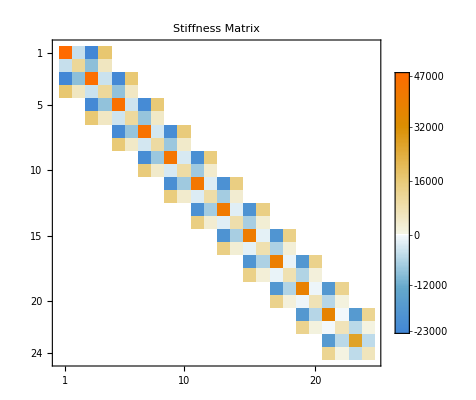

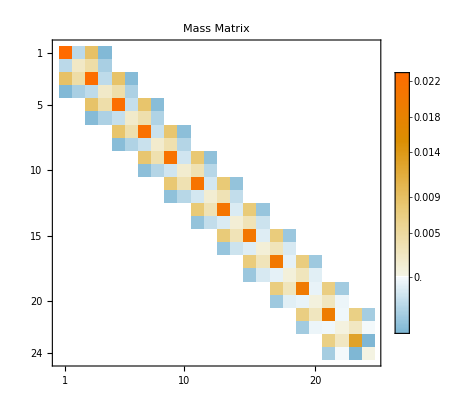

```mathematica
(*matrix Plot*)
MatrixPlot[mat[[1]],PlotLabel->"Stiffness Matrix",PlotLegends->Automatic]
MatrixPlot[mat[[2]],PlotLabel->"Mass Matrix",PlotLegends->Automatic]
```

### Cantilever Euler-Bernoulli Beam

Table 6 for different taper ratios represent the 1st 10

Table 1: Cantilever - Euler-Bernoulli Beam - uniform (vy=vz=0.0)
Table 2: Cantilever - Euler-Bernoulli Beam - tapered (vy=vz=0.1)
Table 3: Cantilever - Euler-Bernoulli Beam - tapered (vy=vz=0.3)
Table 4: Cantilever - Euler-Bernoulli Beam - tapered (vy=vz=0.5)
Table 5: Cantilever - Euler-Bernoulli Beam - tapered (vy=vz=0.6)
Table 6: Cantilever - Euler-Bernoulli Beam - tapered (vy=vz=0.8)

Figures (speed ratio vs frequency) first 6th modes
Fig 1: Cantilever - Euler-Bernoulli and Timoshemko Beams - uniform (vy=vz=0.0) 
Fig 2: Cantilever - Euler-Bernoulli and Timoshemko Beams - tapered (vy=vz=0.2) 
Fig 3: Cantilever - Euler-Bernoulli and Timoshemko Beams - tapered (vy=vz=0.5) 
Fig 4: Cantilever - Euler-Bernoulli and Timoshemko Beams - tapered (vy=vz=0.7) 

Figures (taper ratio vs frequency) first 6th modes at fixed speed
Fig 5: Cantilever - Euler-Bernoulli and Timoshemko Beams - η = 0 (non rotating) 
Fig 6: Cantilever - Euler-Bernoulli and Timoshemko Beams - η = 2.0
Fig 7: Cantilever - Euler-Bernoulli and Timoshemko Beams - η = 5.0
Fig 8: Cantilever - Euler-Bernoulli and Timoshemko Beams - η = 10.0

```mathematica
(*calcuations for Table showing value of frequencies of 6 different taper ratios represent the 1st 10 modes
*) (**file storage is used to avoid repeat computations in case the format for display or export need to be changed*)

Nus={0,0.1,0.3,0.5,0.6,0.8};
Table[
Print["calcuating for ν=" <>ToString[Nu]];
With[{a=0.08, μ=0.3,ki=0.85, νy=Nu,νz=Nu,nelems=12,L=1,Ψ=0,btype="CF",ttype="Euler"},
etas={0,1,3,5,7,10};
Timing[etim=ParallelTable[
mat=N@Assemble[nelems,μ,ki,νy,νz,Ψ,η,a,L,btype,ttype];
eigs=Sort@Eigenvalues[mat],
   {η, etas}];]//Print;
λ = Sqrt[etim];
(**store data in file to avoid rerunning*)
Export["./freq_Euler_tab1to6_"<>ToString[Nu]<>".dat",λ];
],{Nu,Nus}]
```

calcuating for ν=0

{0.509037,Null}

calcuating for ν=0.1

{0.56738,Null}

calcuating for ν=0.3

{0.512577,Null}

calcuating for ν=0.5

{0.48571,Null}

calcuating for ν=0.6

{0.507861,Null}

calcuating for ν=0.8

{0.461886,Null}

{Null,Null,Null,Null,Null,Null}

```mathematica
(**display the tables*)

Nus={0,0.1,0.3,0.5,0.6,0.8};etas={0,1,3,5,7,10};



Table[(**import data*)
λ=Import["./freq_Euler_tab1to6_"<>ToString[Nu]<>".dat"];
heading="Table "<> ToString[Position[Nus,Nu][[1]][[1]]]<>": Cantilever - Euler-Bernoulli Beam - "<>
If[Nu==0,"uniform","tapered"]<>" ("<>ToString[ν]<>" = "<>ToString[Nu]<>")\n";
rowheading=Table[StringJoin["η=",ToString[etas[[i]]]],{i,1,Length[etas]}];
columnheading=Table[Subscript["λ",i],{i,1,10}];
tab=TableForm[λ[[All, 1 ;; 10]], 
 TableSpacing -> {5, 3},TableHeadings -> {rowheading, columnheading}];
Column[{heading,tab//TableForm,"\n"}],{Nu,Nus}]//Column
```

Table 1: Cantilever - Euler-Bernoulli Beam - uniform (ν = 0)

 | λ_1 | λ_2 | λ_3 | λ_4 | λ_5 | λ_6 | λ_7 | λ_8 | λ_9 | λ_10
η=0 | 6.2507 | 39.1731 | 109.698 | 215.037 | 355.751 | 532.211 | 745.13 | 995.604 | 1285.07 | 1614.82
η=1 | 6.48563 | 39.4159 | 109.916 | 215.251 | 355.961 | 532.419 | 745.337 | 995.81 | 1285.27 | 1615.03
η=3 | 8.08899 | 41.3069 | 111.647 | 216.947 | 357.639 | 534.084 | 746.992 | 997.456 | 1286.91 | 1616.65
η=5 | 10.478 | 44.8427 | 115.033 | 220.301 | 360.97 | 537.399 | 750.292 | 1000.74 | 1290.18 | 1619.9
η=7 | 13.1304 | 49.6482 | 119.936 | 225.239 | 365.91 | 542.332 | 755.214 | 1005.65 | 1295.07 | 1624.77
η=10 | 17.239 | 58.4496 | 129.741 | 235.386 | 376.191 | 552.669 | 765.568 | 1015.99 | 1305.39 | 1635.05


Table 2: Cantilever - Euler-Bernoulli Beam - tapered (ν = 0.1)

 | λ_1 | λ_2 | λ_3 | λ_4 | λ_5 | λ_6 | λ_7 | λ_8 | λ_9 | λ_10
η=0 | 6.45737 | 38.529 | 106.36 | 207.714 | 343.099 | 512.871 | 717.71 | 958.657 | 1237.07 | 1554.16
η=1 | 6.66206 | 38.7423 | 106.554 | 207.904 | 343.286 | 513.057 | 717.894 | 958.841 | 1237.26 | 1554.34
η=3 | 8.08965 | 40.4076 | 108.095 | 209.417 | 344.782 | 514.542 | 719.371 | 960.309 | 1238.71 | 1555.79
η=5 | 10.283 | 43.5413 | 111.115 | 212.41 | 347.755 | 517.499 | 722.314 | 963.239 | 1241.63 | 1558.68
η=7 | 12.7698 | 47.8358 | 115.498 | 216.822 | 352.167 | 521.903 | 726.707 | 967.616 | 1245.99 | 1563.01
η=10 | 16.6717 | 55.7833 | 124.298 | 225.909 | 361.361 | 531.14 | 735.953 | 976.852 | 1255.2 | 1572.18


Table 3: Cantilever - Euler-Bernoulli Beam - tapered (ν = 0.3)

 | λ_1 | λ_2 | λ_3 | λ_4 | λ_5 | λ_6 | λ_7 | λ_8 | λ_9 | λ_10
η=0 | 6.94206 | 37.2131 | 99.536 | 192.678 | 317.068 | 473.04 | 661.208 | 882.499 | 1138.08 | 1428.82
η=1 | 7.08371 | 37.3613 | 99.6756 | 192.816 | 317.205 | 473.176 | 661.343 | 882.634 | 1138.22 | 1428.95
η=3 | 8.11829 | 38.5254 | 100.786 | 193.914 | 318.296 | 474.262 | 662.424 | 883.71 | 1139.29 | 1430.01
η=5 | 9.82852 | 40.7517 | 102.97 | 196.094 | 320.467 | 476.426 | 664.581 | 885.857 | 1141.42 | 1432.13
η=7 | 11.8825 | 43.8713 | 106.163 | 199.317 | 323.697 | 479.653 | 667.802 | 889.068 | 1144.62 | 1435.3
η=10 | 15.2401 | 49.8174 | 112.649 | 205.998 | 330.453 | 486.44 | 674.596 | 895.854 | 1151.38 | 1442.02


Table 4: Cantilever - Euler-Bernoulli Beam - tapered (ν = 0.5)

 | λ_1 | λ_2 | λ_3 | λ_4 | λ_5 | λ_6 | λ_7 | λ_8 | λ_9 | λ_10
η=0 | 7.55801 | 35.8699 | 92.4763 | 177.001 | 289.834 | 431.291 | 601.924 | 802.532 | 1034.04 | 1296.96
η=1 | 7.63796 | 35.9505 | 92.5566 | 177.082 | 289.915 | 431.373 | 602.006 | 802.614 | 1034.13 | 1297.04
η=3 | 8.24843 | 36.5891 | 93.1966 | 177.73 | 290.567 | 432.027 | 602.661 | 803.268 | 1034.78 | 1297.68
η=5 | 9.34523 | 37.8337 | 94.4633 | 179.019 | 291.867 | 433.332 | 603.968 | 804.574 | 1036.08 | 1298.97
η=7 | 10.7732 | 39.6268 | 96.3316 | 180.935 | 293.805 | 435.282 | 605.923 | 806.529 | 1038.03 | 1300.9
η=10 | 13.2827 | 43.187 | 100.184 | 184.936 | 297.879 | 439.395 | 610.055 | 810.666 | 1042.15 | 1305.


Table 5: Cantilever - Euler-Bernoulli Beam - tapered (ν = 0.6)

 | λ_1 | λ_2 | λ_3 | λ_4 | λ_5 | λ_6 | λ_7 | λ_8 | λ_9 | λ_10
η=0 | 7.93596 | 35.1965 | 88.8414 | 168.862 | 275.642 | 409.494 | 570.936 | 760.698 | 979.589 | 1228.25
η=1 | 7.99017 | 35.2498 | 88.8965 | 168.919 | 275.699 | 409.552 | 570.994 | 760.756 | 979.647 | 1228.3
η=3 | 8.4112 | 35.6732 | 89.336 | 169.372 | 276.159 | 410.016 | 571.46 | 761.223 | 980.112 | 1228.77
η=5 | 9.19489 | 36.505 | 90.2083 | 170.273 | 277.076 | 410.942 | 572.392 | 762.156 | 981.042 | 1229.69
η=7 | 10.2573 | 37.7174 | 91.5002 | 171.616 | 278.446 | 412.327 | 573.785 | 763.552 | 982.434 | 1231.07
η=10 | 12.2072 | 40.1694 | 94.1829 | 174.432 | 281.333 | 415.254 | 576.735 | 766.511 | 985.386 | 1234.


Table 6: Cantilever - Euler-Bernoulli Beam - tapered (ν = 0.8)

 | λ_1 | λ_2 | λ_3 | λ_4 | λ_5 | λ_6 | λ_7 | λ_8 | λ_9 | λ_10
η=0 | 8.90496 | 33.8938 | 81.3242 | 151.799 | 245.717 | 363.393 | 505.281 | 671.996 | 864.429 | 1085.75
η=1 | 8.94643 | 33.9632 | 81.3971 | 151.871 | 245.787 | 363.461 | 505.347 | 672.06 | 864.49 | 1085.81
η=3 | 9.26756 | 34.5088 | 81.9765 | 152.444 | 246.344 | 364.002 | 505.873 | 672.571 | 864.976 | 1086.25
η=5 | 9.86094 | 35.5512 | 83.1134 | 153.578 | 247.452 | 365.08 | 506.924 | 673.591 | 865.949 | 1087.12
η=7 | 10.6568 | 37.0082 | 84.7659 | 155.254 | 249.099 | 366.69 | 508.495 | 675.12 | 867.407 | 1088.44
η=10 | 12.0982 | 39.7656 | 88.0839 | 158.713 | 252.545 | 370.078 | 511.815 | 678.359 | 870.502 | 1091.23

```mathematica
(*
Fig 1-4: Cantilever - Figures (speed ratio vs frequency) first 6 modes (vy=vz=0,0.2,0.5,0.7) 
*)

Nus={0,0.2,0.5,0.7};
Table[
Print["calculating for ν=" <>ToString[Nu]];
With[{a=0.08, μ=0.3,ki=0.85, νy=Nu, νz=Nu,L=1,Ψ=0,btype="CF"},
(*Calculation of frequencies for Euler beam*)
With[{nelems=12,ttype="Euler"},
etas=Table[i,{i,0,12}];
Timing[eul=ParallelTable[
mat=N@Assemble[nelems,μ,ki,νy,νz,Ψ,η,a,L,btype,ttype];
eigs=Sqrt@Sort@Eigenvalues[mat],
   {η, etas}];]//Print;
];
Print["Euler beam calculated...calculating Timo beam"];
(*Calculation of frequencies for Timoshenko beam*)
With[{nelems=25,ttype="Timo"},
etas=Table[i,{i,0,12}];
Timing[tim=ParallelTable[
mat=N@Assemble[nelems,μ,ki,νy,νz,Ψ,η,a,L,btype,ttype];
eigs=Sqrt@Sort@Eigenvalues[mat],
   {η, etas}];]//Print;
];
];
(**store data in file to avoid rerunning*)
Export["./freq_Euler_fig1to4_"<>ToString[Nu]<>".dat",eul];
Export["./freq_Timo_fig1to4_"<>ToString[Nu]<>".dat",tim];
,{Nu,Nus}]
```

calculating for ν=0

{1.88366,Null}

Euler beam calculated...calculating Timo beam

{1.6576,Null}

calculating for ν=0.2

{1.02516,Null}

Euler beam calculated...calculating Timo beam

{4.96473,Null}

calculating for ν=0.5

{0.985866,Null}

Euler beam calculated...calculating Timo beam

{4.91295,Null}

calculating for ν=0.7

{0.989026,Null}

Euler beam calculated...calculating Timo beam

{5.27899,Null}

{Null,Null,Null,Null}

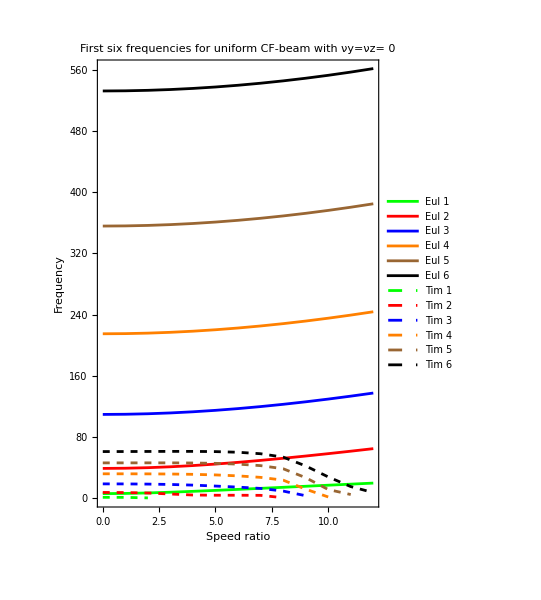
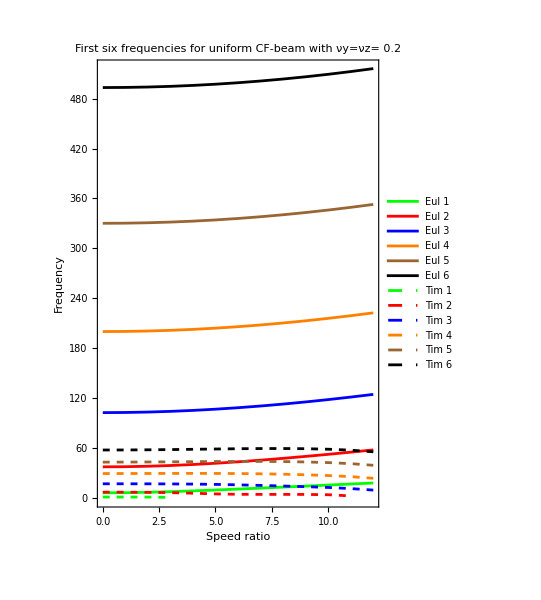
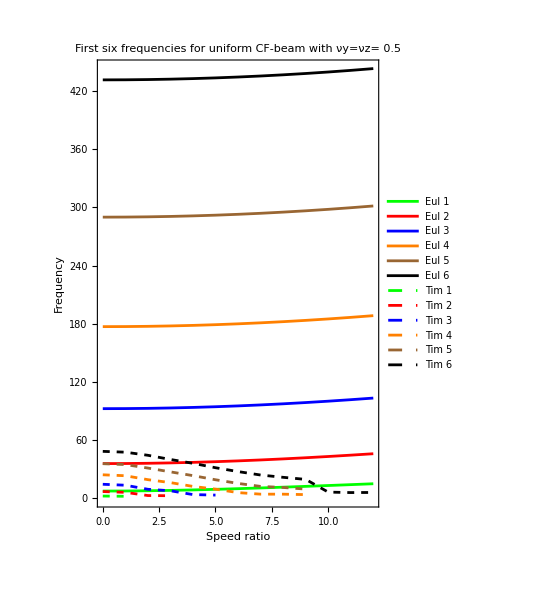
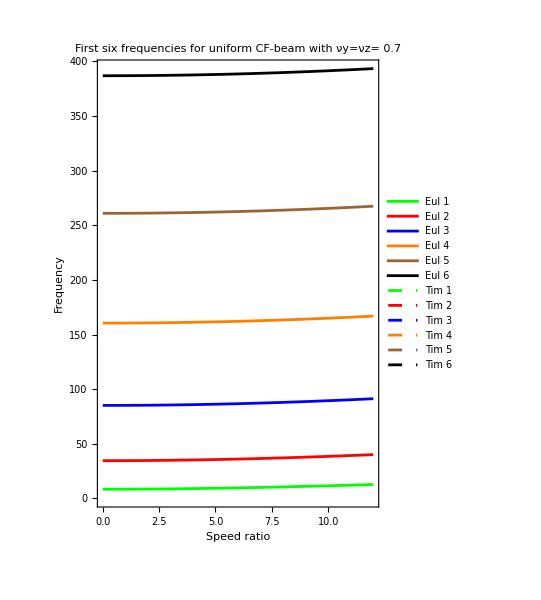

```mathematica
(* plotting
Fig 1-4: Cantilever - Euler-Bernoulli and Timoshemko Beams - for different values of taper ratios (vy=vz=0,0.2,0.5,0.7) 
*)
Nus={0,0.2,0.5,0.7};
plots=Table[
{eul,tim}={Import["./freq_Euler_fig1to4_"<>ToString[Nu]<>".dat"],Import["./freq_Timo_fig1to4_"<>ToString[Nu]<>".dat"]};
modes=Range[6];
plotlabel="First six frequencies for uniform CF-beam with νy=νz= "<>ToString[Nu]<>"\n";
colors={Green,Red,Blue,Orange,Brown,Black};
labels=Join["Eul "<>ToString[#]&/@modes,"Tim "<>ToString[#]&/@modes];
ListLinePlot[Join[Thread[{etas,eul[[All,#]]}]&/@modes,Thread[{etas,tim[[All,#]]}]&/@modes]
 , PlotStyle -> Join[colors,Thread[{Table[Dashed,{i,modes}],colors}]],
 FrameLabel -> {"Speed ratio", "Frequency"}, 
 PlotLegends ->labels,
 PlotLabel -> plotlabel,Frame->True,AspectRatio->1.5]
 ,{Nu,Nus}];
plots
```

```mathematica
(*Calculations for Figures 5 to 8
Figures (taper ratio vs frequency) first 6 modes at fixed speed η=0,2,5,10*)
etas={0,2,5,10};
Table[
Print["calculating for η=" <>ToString[eta]];

(*Calculation of frequencies for Euler beam*)
With[{a=0.08, η=eta,μ=0.3,ki=0.85,L=1,Ψ=0,btype="CF"},
With[{nelems=12,ttype="Euler"},
Nus=Table[ν,{ν,0,0.9,0.1}];
Timing[eul=ParallelTable[
mat=N@Assemble[nelems,μ,ki,νy=ν,νz=ν,Ψ,η,a,L,btype,ttype];
eigs=Sqrt@Sort@Eigenvalues[mat],
   {ν, Nus}];]//Print;
];
Print["Finished calculating for Euler beam...calculating for Timoshenko Beam"];
(*Calculation of frequencies for Timoshenko beam*)
With[{nelems=25,ttype="Timo"},
Nus=Table[ν,{ν,0,0.9,0.1}];
Timing[tim=ParallelTable[
mat=N@Assemble[nelems,μ,ki,νy=ν,νz=ν,Ψ,η,a,L,btype,ttype];
eigs=Sqrt@Sort@Eigenvalues[mat],
   {ν, Nus}];]//Print;
];
];
Export["./freq_Euler_fig5to8_eta"<>ToString[eta]<>".dat",eul]
Export["./freq_Timo_fig5to8_eta"<>ToString[eta]<>".dat",tim]
,{eta,etas}]
```

calculating for η=0

{0.621897,Null}

Finished calculating for Euler beam...calculating for Timoshenko Beam

{3.12968,Null}

calculating for η=2

{0.616276,Null}

Finished calculating for Euler beam...calculating for Timoshenko Beam

{3.64706,Null}

calculating for η=5

{0.746541,Null}

Finished calculating for Euler beam...calculating for Timoshenko Beam

{3.75589,Null}

calculating for η=10

{0.774965,Null}

Finished calculating for Euler beam...calculating for Timoshenko Beam

{3.99255,Null}

{./freq_Euler_fig5to8_eta0.dat ./freq_Timo_fig5to8_eta0.dat,./freq_Euler_fig5to8_eta2.dat ./freq_Timo_fig5to8_eta2.dat,./freq_Euler_fig5to8_eta5.dat ./freq_Timo_fig5to8_eta5.dat,./freq_Euler_fig5to8_eta10.dat ./freq_Timo_fig5to8_eta10.dat}

ListLinePlot::ioproc: {{0.,0.679371},{0.1,1.1815},{0.2,1.58371},{0.3,1.93637},{0.4,2.21795},{0.5,0.+19.91205429494201*I},{0.6,0.+1580.1094571561086*I},{0.7,0.+7042.38739443087*I},{0.8,0.+3780.8388503871297*I},{0.9,0.+3511.4209239530687*I}} may contain non-machine-precision numbers, complex numbers, or invalid entries.

ListLinePlot::ioproc: {{0.,7.04787},{0.1,7.14208},{0.2,7.28013},{0.3,7.42675},{0.4,7.36558},{0.5,2.952},{0.6,0.+585.4862962975144*I},{0.7,0.+3760.633775319108*I},{0.8,0.+2949.768513045957*I},{0.9,0.+1451.2689379710155*I}} may contain non-machine-precision numbers, complex numbers, or invalid entries.

ListLinePlot::ioproc: {{0.,18.6906},{0.1,18.102},{0.2,17.4938},{0.3,16.8431},{0.4,15.8858},{0.5,9.39509},{0.6,0.+247.2587588333906*I},{0.7,0.+2091.9016916735227*I},{0.8,0.+1437.2534358277098*I},{0.9,0.+841.0220886893904*I}} may contain non-machine-precision numbers, complex numbers, or invalid entries.

General::stop: Further output of ListLinePlot::ioproc will be suppressed during this calculation.

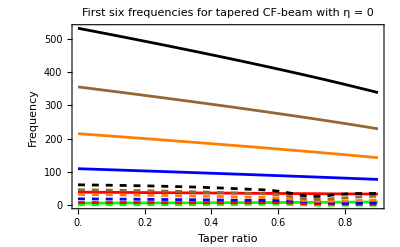
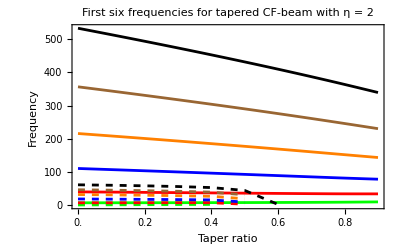
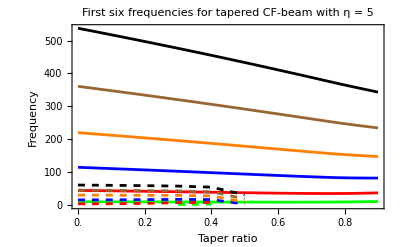
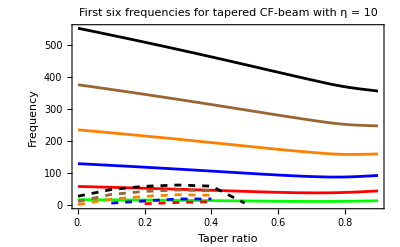

```mathematica
(**Plotting Figure 5 to 8*)
etas={0,2,5,10};
Nus=Table[ν,{ν,0,0.9,0.1}];
plots=Table[
eul=Import["./freq_Euler_fig5to8_eta"<>ToString[eta]<>".dat"];
tim=Import["./freq_Timo_fig5to8_eta"<>ToString[eta]<>".dat"];
modes=Range[6];
colors={Green,Red,Blue,Orange,Brown,Black};
labels=Join["Eul "<>ToString[#]&/@modes,"Tim "<>ToString[#]&/@modes];
ListLinePlot[Join[Thread[{Nus,eul[[All,#]]}]&/@modes,Thread[{Nus,tim[[All,#]]}]&/@modes]
 , PlotStyle ->  Join[colors,Thread[{Table[Dashed,{i,modes}],colors}]],
 FrameLabel -> {"Taper ratio", "Frequency"}, 
 PlotLegends ->None,
 PlotLabel -> "First six frequencies for tapered CF-beam with η = "<>ToString[eta]<>"\n",
 Frame->True,InterpolationOrder->2,FrameTicks->{Automatic,{Nus,None}}]
,{eta,etas}];plots
```

```mathematica
(***waterfall plot**)
(* plotting Fig 1-4: Cantilever - Euler-Bernoulli and Timoshemko Beams - uniform (vy=vz=0,0.2,0.5,0.7) 
*)
(**Assimilating data*)
Nus={0,0.2,0.5,0.7};
etas=Table[i,{i,0,12}];
colors={Green,Red,Blue,Orange,Brown,Black};
modes=Range[6];labels=Join["Eul "<>ToString[#]&/@modes,"Tim "<>ToString[#]&/@modes];
data={};
style={};
Table[
{eul,tim}={Import["./freq_Euler_fig1to4_"<>ToString[Nu]<>".dat"],Import["./freq_Timo_fig1to4_"<>ToString[Nu]<>".dat"]};
data=Join[data,Join[Thread[{etas,Nu,eul[[All,#]]}]&/@modes,Thread[{etas,Nu,tim[[All,#]]}]&/@modes]];
style=Join[style,Join[colors,Thread[{Table[Dashed,{i,modes}],colors}]]];
 ,{Nu,Nus}];
 (*plotting*)
 plotlabel="First six frequencies for CF-beam";
 plot=ListLinePlot3D[data
 , PlotStyle -> style ,Boxed->True,
 PlotLegends ->None,AxesLabel->{"η","ν","λ"},ViewVertical->{0,0,1},
 PlotLabel -> "First six frequencies for tapered CF-beam",Ticks->{Take[etas,{1,Length[etas],2}],Nus,Automatic},
 FaceGrids->{{0,0,-1},{-1,0,0},{0,1,0}},PlotRangePadding->{0.1,0.025,0.1},BoxRatios->{1.5,2,1}];

leg=LineLegend[colors,labels,LegendLabel->"λ"];Show[GraphicsRow[{plot,leg}]]
```

-Graphics-

```mathematica
(**waterfall plot for Figures 5 to 8*)
(*Cantilever - Euler-Bernoulli and Timoshemko Beams frequency variation with taper ratoio&*)
etas={0,2,5,10};
modes=Range[6];
colors={Green,Red,Blue,Orange,Brown,Black};
labels=Join["Eul "<>ToString[#]&/@modes,"Tim "<>ToString[#]&/@modes];
Nus=Table[ν,{ν,0,0.9,0.1}];
data={};
style={};
Table[
eul=Import["./freq_Euler_fig5to8_eta"<>ToString[eta]<>".dat"];
tim=Import["./freq_Timo_fig5to8_eta"<>ToString[eta]<>".dat"];
style=Join[style,Join[colors,Thread[{Table[Dashed,{i,modes}],colors}]]];
data=Join[data,Join[Thread[{Nus,eta,eul[[All,#]]}]&/@modes,Thread[{Nus,eta,tim[[All,#]]}]&/@modes]];
,{eta,etas}];
(**plotting*)
plot=ListLinePlot3D[data
 , PlotStyle -> style ,Boxed->True,
 PlotLegends ->None,AxesLabel->{"ν","η","λ"},ViewVertical->{0,0,1},
 PlotLabel -> "First six frequencies for tapered CF-beam",Ticks->{Take[Nus,{1,Length[Nus],2}],etas,Automatic},
 FaceGrids->{{0,0,-1},{-1,0,0},{0,1,0}},BoxRatios->{1.5,2,1}];
 leg=LineLegend[colors,labels,LegendLabel->"λ"];
 plot58=Show[GraphicsRow[{plot,leg}]]
```

-Graphics-

### Hinged Free Euler-Bernoulli Beam

Table 12 in the paper 

Table 1: Hinged Free Euler-Bernoulli Beam - uniform (vy=vz=0.0)
Table 2: Hinged Free Euler-Bernoulli Beam - tapered (vy=vz=0.1)
Table 3: Hinged Free Euler-Bernoulli Beam - tapered (vy=vz=0.3)
Table 4: Hinged Free Euler-Bernoulli Beam - tapered (vy=vz=0.5)
Table 5: Hinged Free Euler-Bernoulli Beam - tapered (vy=vz=0.7)
Table 6: Hinged Free Euler-Bernoulli Beam - tapered (vy=vz=0.9)

Figures (speed ratio vs frequency) first 6th modes
Fig 1: Hinged Free - Euler-Bernoulli and Timoshemko Beams - uniform (vy=vz=0.0) 
Fig 2: Hinged Free - Euler-Bernoulli and Timoshemko Beams - tapered (vy=vz=0.1) 
Fig 3: Hinged Free - Euler-Bernoulli and Timoshemko Beams - tapered (vy=vz=0.3) 
Fig 4: Hinged Free - Euler-Bernoulli and Timoshemko Beams - tapered (vy=vz=0.5) 
Fig 5: Hinged Free - Euler-Bernoulli and Timoshemko Beams - tapered (vy=vz=0.7) 

Figures (taper ratio vs frequency) first 6th modes at fixed speed
Fig 5: Hinged Free - Euler-Bernoulli and Timoshemko Beams - η = 0 (non rotating) 
Fig 6: Hinged Free - Euler-Bernoulli and Timoshemko Beams - η = 1.0
Fig 7: Hinged Free - Euler-Bernoulli and Timoshemko Beams - η = 3.0
Fig 8: Hinged Free - Euler-Bernoulli and Timoshemko Beams - η = 10.0

## Timoshenko Beam

In addition to the constant parameter  √(ρA_0 L^4/E I_0), in Timoshenko beam theory, there are two further parameters expressing the slenderness ratio and cross sectional properties of the beam. 

The first, related to the slenderness ratio, can be expressed as r_g/L where r_g=√(I_0/A_0) is the radius of gyration of the cross-section, and L is the length of the whole beam. 

The second independent variable is the product G k’. Since G/E maybe taken as a material constant (which varies little between materials). k’ may be regarded as the second variable. the values of k’ are governed by purely geometric considerations and are given by equations:

k'=(10 (1+⋁))/(12 + 11 ⋁) 	,	for rectangular cross-section
k'=(6 (1+⋁))/(7 + 6 ⋁) 	,	for circular cross-section

Poisson’s ratio 		= 0.3
Beam length 			= 0.08
Shear correction factor 	= 0.85
r_g 					= 0.08
Z_0 					= √12 (0.08 L) 

However, in order to reproduce the same result of Downs, the beam dimensions used are:
L 			= 	1 		m
Z_0			= 	0.277128 	m
Y_0	= Z_0/3 	=	0.092376 	m

```mathematica
(**testing for Timoshenko beam *)

With[{a=0.08, η=0.1, μ=0.3,ki=0.85, νy=0.1, νz=0.1,nelems=25,L=1,Ψ=0,btype="CF",TheoryType="Timo"},
mat=Assemble[nelems,μ,ki,νy,νz,Ψ,η,a,L,btype,TheoryType];//Timing//Print;
eigs=Eigenvalues[mat];
eigs//Sqrt//Sort//Print;]
```

{23.4119,Null}

{1.50925,7.65947,18.3078,31.0851,45.1202,59.8635,75.0309,90.1661,101.735,104.461,114.734,119.866,131.362,137.331,149.594,156.58,168.744,177.157,188.919,198.454,210.473,219.975,233.663,241.594,258.256,263.538,282.689,287.036,305.028,313.292,326.529,338.884,348.851,359.147,371.997,376.858,385.047,388.448,409.337,440.268,472.193,504.16,535.463,565.333,592.924,617.363,637.839,653.699,664.547,668.774}

### Cantilever Timoshenko Beam

```mathematica
(*Calculation of frequencies for Timoshenko beam*)
With[{a=0.08, μ=0.3,ki=0.85, νy=0.1, νz=0.1,nelems=25,L=1,Ψ=0,btype="CF",TheoryType="Timo"},i=.;
etas=Table[i,{i,0,12}];
Timing[tim=ParallelTable[
mat=N@Assemble[nelems,μ,ki,νy,νz,Ψ,η,a,L,btype,TheoryType];
eigs=Sqrt@Sort@Eigenvalues[mat,Method->{"FEAST",Interval->{1,10^9}}],
   {η, etas}];]//Print;
];
```

{6.06518,Null}

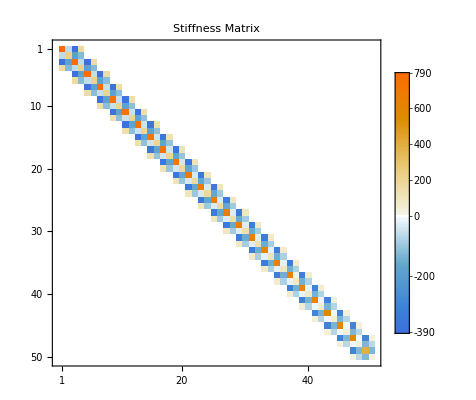

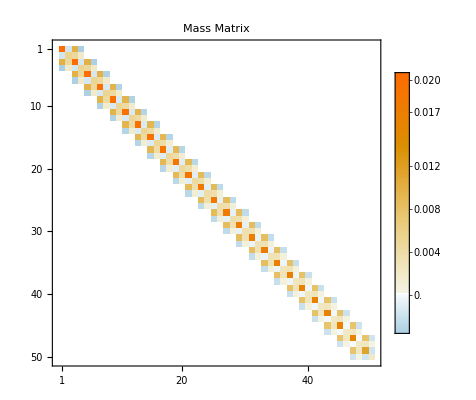

```mathematica
(*matrix Plot*)
MatrixPlot[mat[[1]],PlotLabel->"Stiffness Matrix",PlotLegends->Automatic]
MatrixPlot[mat[[2]],PlotLabel->"Mass Matrix",PlotLegends->Automatic]
```

### Hinged Timoshenko Beam

```mathematica
(*Calculation of frequencies for Timoshenko beam*)
With[{nelems=25,TheoryType="Timo",btype="HF",a=0.08, μ=0.3,ki=0.85, νy=0.1, νz=0.1,L=1,Ψ=0},
etas=Table[i,{i,0,12}];
Timing[tim=ParallelTable[
mat=N@Assemble[nelems,μ,ki,νy,νz,Ψ,η,a,L,btype,TheoryType];
eigs=Sqrt@Sort@Eigenvalues[mat,Method->{"FEAST",Interval->{1,10^9}}],
   {η, etas}];]//Print;
];
```

{5.5894,Null}

```mathematica
eigs
```

{447258.,441623.,427322.,406839.,381137.,351559.,319601.,286721.,254177.,222966.,193836.,167557.,150892.,148262.,142022.,138382.,128986.,121697.,114843.,106621.,98151.6,93042.2,82389.7,79913.3,69452.1,66696.2,58367.4,54598.2,48388.9,44298.7,39383.9,35690.4,31384.6,28474.6,24517.2,22378.4,18859.9,17256.1,14367.9,13164.,10912.1,10349.9,8129.92,5629.63,3583.64,2035.83,966.285,335.177,58.6675,2.27782}